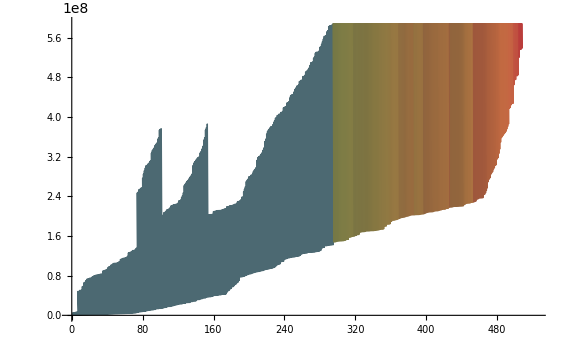

```mathematica
With[{p=3,q=5},
ListLinePlot[Monitor[
Sort[
Flatten[
Table[
TableIze[BinRatio[p,q,i,j,1000000000000]]
,{i,0,p-1},{j,0,q-1}
],2
]]
,{i,j}
],
PlotStyle->PointSize[Small],
Mesh->None,
ColorFunction->"DarkRainbow"
]
]
```

```mathematica
All35=With[{p=3,q=5},
Sort[
Flatten[
Table[
BinRatio[p,q,i,j,1000000000000]
,{i,0,p-1},{j,0,q-1}
],2
]]
]
```

{390,585,1170,1440,2220,3090,4410,4770,5235,5595,6030,6390,9870,13665,14595,14610,15270,15465,28485,29925,31155,31740,32385,36465,37695,38910,40140,42210,43440,44655,45615,45885,46845,48075,54585,55095,56325,61275,63915,65100,70575,71445,78525,82350,83715,87195,93090,94590,95655,102120,104700,114015,117840,119775,135930,142260,154065,174450,183780,184740,200400,225765,229590,231075,231645,241350,297975,312435,334260,365070,380130,402810,406725,407595,409020,421815,426600,431460,475200,494205,495075,501075,518355,532845,533460,536175,552510,563565,566655,573675,580965,594270,604155,609705,614445,641085,647205,649080,651270,652875,676680,678585,686580,689295,719775,724800,726795,742980,757275,762825,771900,772710,794205,800325,802200,803835,804390,806010,831705,839040,839700,842415,869730,872895,887160,900435,901245,910395,922305,930900,943515,947325,949065,957210,963765,970260,981015,984825,995535,1022535,1026015,1042830,1063515,1078875,1084665,1092900,1096635,1100445,1116900,1119570,1134135,1137945,1148655,1179135,1195965,1207410,1216215,1216635,1228500,1237065,1249755,1253565,1255260,1263405,1270035,1276425,1287255,1291860,1301775,1332255,1349100,1365600,1369755,1377225,1402875,1404960,1414725,1417500,1423080,1440375,1441635,1445040,1473960,1476780,1494195,1513590,1522395,1530345,1543230,1555995,1567845,1582590,1593495,1594770,1598160,1600710,1602495,1629915,1647330,1653285,1671765,1675950,1683465,1709115,1711125,1720965,1723695,1729245,1746615,1747905,1751280,1780125,1781820,1783050,1800465,1819785,1828590,1834110,1836585,1857285,1866090,1874085,1876800,1904400,1908660,1914300,1929825,1949745,1959450,1972905,1977945,1981710,1982130,1989705,2010405,2019210,2027205,2029920,2035410,2056980,2057520,2067420,2086290,2087985,2092185,2102880,2126025,2134830,2140305,2142825,2163525,2172330,2180325,2183040,2210640,2214825,2236020,2256015,2279145,2284140,2287950,2288295,2316645,2320005,2321640,2325450,2336160,2337810,2339700,2345385,2346045,2372715,2382885,2402745,2416830,2432265,2437260,2441070,2463975,2469765,2474760,2478570,2481645,2489280,2492835,2494380,2498505,2508405,2516550,2536005,2585385,2590380,2594190,2594460,2622885,2627880,2631690,2642400,2644005,2645970,2651625,2652240,2678910,2688060,2689125,2708910,2722995,2743500,2744865,2755350,2757135,2770140,2773650,2775540,2781000,2788260,2791065,2794635,2804745,2818965,2837445,2842245,2870970,2878770,2896620,2898675,2907225,2908470,2910255,2916795,2926785,2934120,2944200,2945805,2947500,2947755,2957865,2976840,2995365,3015075,3024090,3049740,3051060,3061590,3063375,3074340,3076305,3079920,3081735,3087240,3094425,3097335,3100875,3110985,3125130,3143610,3148485,3177210,3214710,3216495,3217425,3222960,3231090,3246615,3251970,3253665,3253995,3254925,3285990,3295005,3310125,3323460,3330330,3367830,3369615,3370545,3380505,3393450,3399750,3407115,3408045,3431295,3439125,3467295,3475845,3483450,3520950,3522735,3523665,3529125,3537285,3552885,3558135,3559830,3560235,3561165,3592260,3616320,3629655,3636570,3660060,3673395,3676785,3734790,3747825,3751635,3761550,3763365,3782010,3789135,3789705,3829905,3875610,3896460,3897150,3904755,3905385,3910185,3910545,3916500,3942255,3942840,3979560,3983025,4024995,4040985,4053240,4054020,4057875,4067745,4069635,4082475,4088175,4095375,4095975,4108095,4126215,4131915,4133355,4140720,4160370,4163385,4200885,4202625,4210995,4223655,4229985,4248495,4285725,4290810,4303845,4304205,4313010,4316505,4331160,4354005,4364115,4376790,4401615,4414260,4419345,4432380,4439520,4466565,4469625,4507125,4508790,4517235,4529925,4536180,4554735,4563270,4568055,4596270,4596975,4610010,4622745,4624725,4641525,4660245,4698570,4725510,4738545,4745685,4768560,4775865,4793670,4797960,4802430,4838520,4858680,4859805,4919265,4936995,4941285,4943940,4945755,4967955,4979190,5002005,5047155,5099385,5111280,5121930,5122515,5179590,5253120,5257410,5297970,5378715,5379435,5396445,5400735,5403390,5405205,5427405,5438640,5461455,5493195,5501745,5504970,5519940,5560515,5572215,5641575,5641935,5645070,5703840,5762640,5844195,5855895,5860185,5862840,5864655,5892885,5920905,5961195,6019965,6101025,6104520,6109380,6163290,6303645,6315345,6319635,6322290,6324105,6352335,6375420,6380355,6423645,6490890,6495660,6560475,6563970,6568830,6622740,6703800,6763095,6774795,6779085,6781740,6783555,6811785,6839805,6885285,6978615,6982020,6983130,7014720,7019925,7020585,7023420,7028280,7046100,7163250,7189425,7234245,7247220,7299255,7300455,7336905,7344735,7377570,7415925,7441470,7442580,7474170,7479375,7482870,7485645,7487730,7505550,7622700,7648875,7693695,7706670,7758705,7802505,7804185,7820010,7837020,7900920,7902030,7933620,7939260,7942320,7947180,7965000,8028675,8076945,8082150,8085645,8108325,8142495,8166120,8225490,8261940,8263635,8284770,8333010,8366400,8369055,8370870,8393070,8401770,8406960,8421090,8465775,8536395,8541600,8545095,8564415,8618625,8723085,8734680,8744220,8761950,8792460,8825850,8828505,8830320,8861220,8864295,8866410,8880540,8995845,9001050,9001260,9004545,9019185,9023865,9078075,9144165,9203670,9204390,9221400,9266325,9271950,9285300,9287955,9289770,9325860,9339990,9431280,9455295,9460500,9463995,9483315,9680850,9726540,9744750,9749220,9792870,9900225,9907335,10004400,10022415,10037205,10101090,10133895,10196940,10263735,10275615,10308420,10370115,10402920,10470690,10488780,10500075,10512930,10521585,10532880,10567350,10588560,10591395,10600275,10611555,10621365,10623945,10670070,10702875,10711140,10770600,10831455,10910130,10942935,10956330,10995315,11028120,11087745,11191950,11209935,11219175,11224755,11288610,11321415,11372460,11400600,11528070,11644665,11677470,11754870,11756145,11776080,11778915,11787795,11808885,11857590,11890395,11907510,11915865,11940315,11948670,11964480,11994450,12015690,12027255,12048495,12105930,12127170,12197685,12230490,12397440,12406695,12422430,12435105,12455235,12476115,12508920,12588120,12614280,12715590,12728220,12758235,12813750,12832185,12845805,12864990,12943665,12975300,13062990,13095030,13127835,13181970,13203210,13214775,13236015,13239060,13293450,13314690,13337880,13416555,13419570,13449360,13622625,13663635,13696440,13701300,13734105,13775640,13801800,13901955,13915740,13983120,14001270,14011590,14051460,14084265,14098590,14162820,14279100,14333280,14393985,14472660,14505465,14525400,14604075,14636880,14743770,14772540,14805345,14810145,14822445,14851155,14855250,14883960,14888820,14921625,14963160,15041835,15074640,15104325,15110085,15125565,15137130,15158370,15188775,15225435,15323655,15437925,15509685,15581505,15619350,15632070,15660180,15664875,15691710,15692985,15724350,15745545,15770385,15913890,15931290,15946695,15997665,16009965,16030230,16042770,16076340,16087545,16109145,16112895,16126260,16145700,16159065,16204980,16376295,16394715,16412955,16427520,16437645,16470450,16506195,16549125,16625445,16697205,16731105,16806870,16833030,17157195,17275065,17300445,17310255,17313780,17333250,17346585,17370765,17410635,17443440,17563815,17582265,17600475,17615070,17679150,17692455,17693715,17711955,17736645,17759850,17838525,17845095,17871330,17877900,17918625,17920020,17952825,18007185,18010965,18020550,18032205,18039990,18119265,18201840,18289005,18321810,18337710,18558315,18807600,18840405,18881235,18912855,18924165,19026045,19058850,19236135,19265640,19287030,19298445,19306785,19328805,19425945,19458750,19526535,19537425,19728435,19995120,20027925,20100375,20192355,20248935,20306295,20336115,20453160,20485965,20539620,20594415,20613465,20646270,20669430,20673090,20692425,20705895,20724945,20881455,20915955,20938845,21151830,21172275,21187860,21220665,21301335,21334140,21375915,21379875,21432150,21464955,21491115,21493815,21540840,21556920,21569790,21573645,21583155,21602595,21635595,21640680,21668400,21673485,21713970,21746775,21752160,21822660,21855465,21860610,21893415,21912465,21934140,22142775,22160865,22193670,22353225,22359795,22442685,22545225,22578030,22657770,22667400,22687980,22706730,22716540,22739535,22744440,22782435,22823115,22855920,22962885,22988550,23020350,23021355,23031450,23041560,23048130,23064255,23074365,23080935,23099985,23121660,23122770,23131605,23155575,23213730,23413470,23422410,23446275,23540745,23557650,23590455,23695290,23728095,23732745,23765550,23845290,24018990,24097665,24130470,24150405,24207870,24229080,24261885,24319125,24489795,24609930,24666810,24699615,24745170,24750540,24777975,24783345,24813780,24850440,24875130,24907935,24911145,24932820,24948630,24966450,24986610,25016610,25045125,25049415,25077930,25091655,25206510,25285185,25298430,25317990,25331235,25349325,25497885,25530690,25541235,25574040,25779705,25790880,25797450,25823055,25855860,25876125,25908930,25922640,26001300,26011680,26037960,26141610,26153970,26154390,26232645,26265450,26356110,26394015,26444625,26472690,26477430,26505495,26532180,26564985,26588880,26621685,26656860,26726445,26735535,26759250,26768340,26776410,26814000,26846805,26876520,26925435,26958240,26978400,27188820,27207255,27225480,27240060,27304155,27336960,27341910,27363630,27442305,27543630,27581535,27585975,27623385,27656190,27660210,27666735,27693015,27699540,27776400,27809205,27844380,27923055,27955860,28025985,28030320,28052460,28058790,28064040,28159395,28188720,28247310,28307805,28340610,28422240,28437735,28470540,28529430,28629825,28729695,28762500,28829280,28854255,28887060,28889865,28890645,28923450,28963920,28996725,29072625,29105430,29184105,29185200,29222010,29263875,29296680,29633085,29650245,29683050,29704290,29812965,29817345,29932065,29953305,29964870,29986110,30016815,30053475,30066765,30078165,30110970,30113895,30145440,30146700,30230400,30260145,30292950,30294405,30371625,30372720,30409530,30451395,30484200,30492615,30598290,30631095,30741810,30774615,30875610,30880110,30904170,30936975,30954285,30987090,31181925,31185990,31260600,31265685,31293405,31298490,31332960,31377165,31479030,31511835,31582380,31661055,31760850,31793655,31821945,31900620,31921020,31929330,31933425,31938465,31962135,31971270,32063130,32141805,32170230,32174610,32203035,32220285,32244705,32253090,32277510,32312955,32369445,32448120,32480925,32489010,32506920,32526525,32539725,32559330,32621760,32712750,32788740,32821545,32838705,32848575,32859945,32871510,32892750,33009465,33047415,33088140,33120945,33357750,33376005,33390555,33401100,33433905,33458745,33556950,33635625,33668430,33782055,33809280,33814860,33935325,33968130,34022490,34036095,34055295,34063875,34096680,34096950,34126485,34234935,34291800,34300170,34324605,34513125,34573620,34706820,34739625,34744470,34793580,34794855,34823145,34827660,34838205,34855950,34871010,34919550,34988640,34998225,35021445,35031030,35076675,35120025,35152830,35422455,35487690,35501130,35533935,35541840,35566365,35574645,35576175,35599170,35695380,35766585,35848185,35866170,35880990,35944845,35977650,35981100,36107070,36161880,36185745,36218550,36384945,36444030,36970515,37007490,37021410,37040295,37213320,37246125,37270530,37291740,37324545,37414470,37480260,37495140,37496715,37527945,37572465,37594725,37747545,37872300,37895295,37983315,38087670,38120475,38250450,38458050,38479260,38512065,38597520,38619195,38630325,38652000,38797740,38847015,38879340,38901015,38912145,38933820,38935065,38938785,38971590,39012330,39035715,39059850,39068520,39317535,39428775,39461580,39542250,39641820,39657285,39678480,39794475,39855375,39877155,39895245,39928050,40019850,40034535,40041060,40098525,40119735,40126305,40152540,40159110,40177065,40199850,40366815,40399620,40401780,40549185,40618920,40829325,40926450,40948125,40981995,41207370,41228580,41286045,41305170,41307255,41322330,41340060,41355135,41446950,41463105,41484885,41525625,41545995,41554335,41558430,41587140,41604150,41636955,41785980,41806440,41937945,41966490,42016845,42021870,42156915,42169515,42169935,42224175,42246765,42248190,42280995,42355005,42416085,42448875,42494760,42506475,42527565,42580290,42634470,42672405,42713145,42745950,42797475,42904260,42937065,42993945,43219830,43614990,43668825,43747500,43926675,44116485,44224365,44250345,44414175,44548035,44569875,44810145,44813460,45130635,45764775,45797925,45817830,45849645,45953625,46062465,46218165,46271220,46309155,46853655,46955310,47046870,47358555,47437230,47678955,47854920,47939610,47976645,47997105,48061890,48132345,48319140,48342780,48393000,48515280,48640470,48697815,48772530,48796035,48853515,48900510,49042080,49080195,49093725,49197780,49255770,49261995,49278360,49327110,49357035,49405410,49446375,49457835,49484085,49495470,49624800,49715385,49755525,49780500,49789455,49891695,49899765,49911225,49986465,49999995,50264835,50343510,50557755,50713425,50796390,50797965,50970900,51011115,51028380,51115155,51219645,51308850,51373965,51375345,51400650,51424290,51485160,51504690,51556350,51671655,51673035,51802380,51938550,51958050,52157535,52289445,52345290,52604580,52610925,52742835,52760280,52798680,52844820,52889610,52919535,53020335,53057970,53164920,53187300,53243595,53298120,53318025,53473725,53615295,53663835,53808975,53829240,53874120,53928225,54117225,54171810,54204390,54256140,54262365,54327510,54405255,54502080,54516435,54702945,54813765,54858645,55142730,55467945,55531335,55546620,55610010,55662150,55720035,55819380,55844190,55927485,56006160,56017725,56049000,56117760,56244585,56329410,56415450,56502390,56559915,56571150,56649015,56697975,56905425,56946705,57013305,57165915,57189585,57203115,57235680,57244590,57323265,57358815,57371385,57385170,57490695,57689070,57700080,57776145,57812205,57824775,57854820,57906225,57997770,58001085,58088760,58095855,58164615,58291440,58376265,58462305,58542150,58549140,58589130,58749120,58900815,58903350,58907355,58952115,58970265,58982025,59048940,59080245,59249805,59291730,59328990,59360625,59370405,59405505,59418240,59484690,59533635,59591235,59594550,59746935,59782380,59790030,59807085,59945730,60044625,60047940,60104775,60133605,60220830,60416460,60474375,60653370,60713925,60740175,60798165,60869625,60922335,60998970,61095855,61127100,61167315,61296660,61322730,61375725,61583070,61736475,61776120,61782540,61918320,62235930,62365530,62371710,62463315,62514615,62544525,62557965,62642745,62713665,62812305,62923125,62974275,63011355,63096135,63110475,63352470,63408165,63427665,63508170,63783330,63829395,64030260,64036875,64115550,64127085,64205070,64227150,64239315,64314435,64317990,64327950,64351065,64353960,64396665,64438770,64483650,64524840,64680540,64767720,64807350,64833900,64916490,65001630,65021130,65047965,65072190,65203665,65345040,65455020,65469195,65480775,65494545,65642730,65673990,65869590,65921595,65934165,65954415,66005595,66008265,66015570,66127380,66271440,66274005,66296835,66322980,66400815,66458985,66571695,66608520,66687195,66698505,66814575,66858465,66860685,67010175,67012740,67091415,67243965,67314075,67401135,67479810,67527645,67697355,67720845,67899420,67916445,68001270,68055120,68187510,68214135,68242950,68266185,68444550,68478960,68525820,68634660,68719065,68742240,68762760,68797740,68897940,69432090,69729780,70041465,70046370,70099365,70291770,70491405,70522590,70547340,70589460,70637310,70789095,70947735,71000730,71088045,71166720,71205480,71245395,71271705,71401125,71540895,71557080,71619570,71698245,71892675,71958900,71959590,71990520,72088320,72218025,72296700,72314415,72336540,72463350,72634230,72687330,72789930,72791760,72867840,72877110,72916740,73157310,73165530,73245150,73313010,73374525,73603935,73661865,73740540,73763130,73783380,73827915,74166150,74236770,74470725,74510205,74603070,74619540,74734185,74782410,74807895,74861085,74900295,74914755,74923965,74939760,74978970,74993430,75021795,75045870,75057645,75124545,75235365,75353310,75510525,75533055,75546585,75589200,75633255,75688755,75806700,75908265,76427745,76506360,77016990,77037915,77169255,77234295,77282220,77304870,77314680,77493075,77524410,77571750,77579910,77680110,77921490,77943390,78024630,78133170,78208755,78344055,78422730,78586560,79271400,79273755,79305975,79369200,79381050,79459035,79592760,79640145,79890450,80068245,80069025,80093535,80099910,80180025,80292345,80356830,80448045,80512530,80713035,80745735,80789400,80791710,80796720,80810220,80870385,81108345,81182070,81406035,81483915,81494085,81505890,81572760,81584565,81651435,81695670,81872475,81937305,82028175,82088340,82305045,82325865,82375080,82490265,82541730,82548255,82619610,82843575,82917300,83001645,83155260,83211315,83228925,83233935,83344755,83462670,83515665,83543820,83642445,83655975,83664705,83742645,83798145,83841510,83854785,83916060,83922645,84010485,84135195,84308175,84351900,84376035,84421935,84432885,84615750,84719220,85031310,85080030,85147305,85255635,85391610,85406415,85434975,85590675,85602465,85633800,85681140,85689300,85709025,85767225,85789500,85793385,85888365,85921890,85937580,86000565,86052750,86104155,86220615,86398590,86453445,86510580,86532120,86546955,86791350,86808270,87085785,87126885,87438570,87453225,87478545,87539175,87568395,87626280,87736260,87758175,88079670,88178460,88211565,88376655,88401735,88445445,88557435,88593810,88642530,88766865,88822425,88855125,88898760,88901100,88954215,88979775,88994205,89031765,89084040,89110440,89217750,89244555,89251905,89291460,89400255,89422125,89429895,89515440,89673135,89805030,89850450,89970825,89981835,90117090,90137535,90158175,90197730,90303840,90327375,90414405,90421710,90435225,90651120,90845370,90859665,91108905,91130895,91157355,91235265,91291410,91298760,91320675,91338315,91340895,91390965,91454145,91562295,91653180,91688655,91751835,91793775,91872450,91907535,91930050,91937325,91947405,91950870,92000085,92106315,92127090,92173275,92327400,92406075,92468565,92559705,92624520,92626665,92780250,92836320,92858925,92881740,93024465,93077910,93087675,93140670,93168825,93289710,93304020,93364980,93466515,93477855,93541065,93564630,93601710,93645705,93724380,93803055,93818370,93821925,93900600,93976905,93979275,93984180,93994260,94046940,94295865,94507980,94532160,94593555,94656315,94705035,94961235,95059980,95195175,95215680,95227455,95306130,95392230,95499825,95513370,95562585,95648565,95759010,95782245,95811510,95845620,96109200,96135570,96171960,96220695,96366375,96433260,96554835,96625140,96676875,96751890,96755550,96834225,96907890,97015470,97063575,97078230,97142235,97167180,97208430,97220910,97287105,97309365,97327140,97361265,97453500,97539240,97624830,97702665,97751190,97807185,97959840,98010075,98026725,98156055,98165775,98182425,98218815,98226435,98267535,98323095,98401770,98413230,98480115,98531100,98556000,98579220,98619210,98625645,98635485,98876910,99079035,99088875,99218295,99344655,99500355,99606840,99671685,99762540,99776070,99783180,99798045,100056795,100060230,100470375,100682340,100923765,100980030,100991085,101278185,101291715,101390355,101413410,101444475,101562330,101575875,101711100,102103650,102197985,102249525,102495675,102543480,102617370,102649470,102660945,102702915,102793830,102807360,102858330,102958635,102960120,103091520,103102860,103114335,103156020,103169340,103304565,103311720,103325040,103609185,103622730,103713630,103757955,103891590,103920870,104167020,104218560,104242815,104244960,104330040,104428005,104532405,104540505,104542650,104553585,104684985,104696205,104707800,104734485,104840685,104850030,104854215,104928705,105005490,105006975,105017235,105124830,105138375,105276525,105418710,105436515,105470625,105538080,105562890,105579585,105658260,105692280,105734205,105860580,105969945,105989970,105991365,106119420,106136115,106145670,106223445,106275120,106291815,106376895,106496970,106521135,106575645,106589505,106596525,106640475,106688580,106900905,106986270,107078490,107141730,107327670,107376180,107439420,107454045,107584830,107588100,107595120,107609745,107739090,107781060,107892540,107907435,107915070,108036780,108038220,108041490,108166185,108181005,108192480,108218835,108260490,108267840,108314280,108415185,108460275,108469980,108527745,108579735,108677790,108713880,108757965,108767670,108913665,108947760,108981135,109033125,109312875,109359420,109401075,109463670,109542345,109932210,110005680,110158995,110265690,110307345,110314695,110317365,110396040,110474715,110574525,110605035,110619405,110781600,110833935,110848635,110860275,110916720,110927310,110967675,111005985,111027915,111265365,111278685,111287325,111380100,111421065,111434385,111443220,111458775,111537450,111732075,111822990,111974520,112120680,112285950,112352160,112432365,112583640,112617600,112624995,112649850,112662930,112739340,112765005,112805550,112843680,112880790,113014530,113071905,113116320,113150580,113229255,113312220,113338635,113467890,113601915,113603460,113682135,113760810,113792025,114055305,114100755,114104025,114125430,114332805,114479220,114530175,114578820,114630495,114742500,114827865,114844365,114876615,114915840,114955290,114983565,114994515,115006320,115010295,115073190,115084995,115151865,115297755,115314690,115380915,115406205,115421955,115463550,115510365,115648770,115694220,115697490,115768080,115834305,115848450,115903260,115963755,116024415,116093400,116146140,116147610,116150880,116180115,116328225,116423625,116579325,116689080,116755305,116789280,116877015,117057150,117131910,117142470,117208695,117311775,117364095,117390450,117422220,117442470,117468810,117476475,117494385,117521145,117573060,117599820,117651735,117661785,117695760,117719910,117817485,117843330,118037055,118041555,118173030,118314495,118626180,118728750,118860225,118931415,118943325,119100450,119131005,119235555,119344815,119384805,119396715,119477160,119489535,119568210,119586915,119642505,119742615,119774850,120083910,120141825,120439515,120507795,120874440,120953115,120953160,120990180,121080045,121181295,121259970,121282410,121338645,121391730,121438110,121470405,121702560,122155950,122178960,122213415,122389980,122468655,122476650,122699655,123088560,123092910,123119685,123247065,123309030,123325740,123415185,123490260,123515550,123775755,123806880,123868575,123943650,124012650,124202745,124260270,124532985,124688685,124864650,124986375,125318040,125349450,125421165,125428125,125450580,125499840,125551860,125606280,125630535,125709210,125749155,125827830,125829270,125850285,125880720,125903970,125952720,126146445,126303675,126343740,126377715,126423855,126533415,126735540,127052715,127067460,127146135,127209840,127224810,127234095,127322355,127344915,127401030,127468830,127479705,127506105,127598970,127662045,127677645,127696260,127741155,127777785,127791390,127851960,127939500,128193300,128231175,128251185,128417385,128481900,128493210,128504700,128548860,128609415,128620035,128775735,128802390,128860560,128946600,128958090,128983875,129062505,129073425,129099585,129256800,129260280,129371565,129391755,129415980,129515685,129547455,129766830,129818235,129916320,130064520,130125060,130213365,130353555,130355790,130432230,130510905,130551555,130666755,130693770,130772445,130806285,130809045,130822590,130849245,130884960,130907415,130924590,130963635,131031330,131063115,131080290,131327565,131337840,131340120,131381820,131416515,131418420,131431965,131495190,131587755,131640705,131780955,131793510,131869200,131947875,132026550,132041145,132338235,132546975,132720030,132947610,133040205,133119915,133173420,133350735,133384845,133386975,133417605,133463520,133468740,133485360,133493595,133542195,133637640,133687560,133853880,133860615,134104230,134151570,134157990,134226300,134313690,134436585,134557620,134611380,134679690,134708985,134734275,134766885,134889975,134902620,134994465,135064575,135150165,135244815,135349725,135454275,135475290,135803115,135887130,135928680,136048860,136151085,136340520,136360545,136418265,136448775,136526730,136547895,136614090,136668915,136682430,136845585,136859100,136871655,136911780,136969920,136980120,136990950,137001285,137067480,137093835,137291595,137366160,137444340,137480955,137876190,137927580,137978790,138198075,138234420,138245040,138400740,138453450,138485565,138495765,138536955,138698430,138782700,138803130,138881805,138906840,138918435,139140690,139180425,139236090,139365585,139371825,139391835,139478115,139541325,139611465,139689525,139750065,139789800,139868475,139923150,139978560,139997400,140052600,140057235,140089230,140133015,140135910,140244930,140255025,140318775,140333700,140397450,140412375,140447595,140532420,140542620,140656335,140688120,140820000,140829420,140965125,141006825,141010110,141056970,141080715,141083325,141236415,141265710,141273390,141276390,141282810,141305445,141384120,141418515,141432090,141490080,141494205,141536715,141572880,141578085,141651555,141729780,141747030,141770625,141849300,141927975,141943470,141963240,141970005,142079310,142171980,142200420,142302180,142335645,142380855,142572615,142631055,142653810,142687770,142766445,142789035,142821090,142876275,142899765,142978965,143009850,143011980,143088525,143167200,143173965,143312565,143478885,143776575,144012615,144091290,144258570,144412710,144527625,144619470,144711960,144775170,145100295,145447755,145553685,145655445,145734120,145745445,146036940,146043270,146351535,146496660,146562795,146646315,146724990,146892045,146991165,147016185,147092925,147289800,147345435,147390615,147546315,147587490,147642180,147678180,147703380,147720855,147731940,147754695,147899175,147977850,148032540,148052385,148161960,148198575,148208085,148354275,148428135,148506810,148609650,148621530,148651965,148736640,148805430,148907340,148938810,149103120,149116185,149192670,149219025,149385735,149392200,149414805,149493480,149541435,149599425,149646060,149677605,149704185,149801550,149839125,149880015,149958690,150037365,150052815,150075150,150079395,150099240,150125295,150153825,150411570,150445005,150490245,150578685,150656640,150688485,150763200,150844185,150898395,150930450,150954330,151009125,151115085,151141725,151240650,151265880,151317195,151568475,151614885,151694040,151767945,152024280,152122005,152179980,152200680,152446095,152455140,152524770,152547795,152703495,152735340,152832840,153001185,153022875,153130530,153142335,153286230,153687810,153693030,153719775,153875475,153883575,153961710,153985500,154040385,154231035,154336965,154728615,154892160,154970835,155155545,155182005,155234220,155399190,155526000,155661945,155811735,155841285,155890410,155976540,156008565,156087240,156271320,156349995,156650070,156728745,156807420,156846030,157225530,157313490,157379700,157468650,157611180,157677390,157766880,157786965,157789380,157833090,158155845,158184540,158186715,158263215,158265390,158609235,158688030,158695665,158718270,158797875,158872590,158953575,159037005,159149055,159226920,159302610,159360345,159375225,159426555,159515505,159658035,159724245,159827190,159833925,159836250,159877290,159879900,159905865,160001730,160070010,160072965,160157430,160202610,160455120,160523400,160564485,160635330,160656000,160740090,160742520,160760160,160844730,160875990,160942200,161151240,161163045,161173680,161193480,161229915,161239890,161251680,161298015,161322315,161615640,161694315,161775705,161813925,161829120,161892600,161984820,162204285,162391635,162457845,162689325,162711510,162755535,162837960,162845025,162911235,163291350,163398705,163586700,163635390,163665375,163875975,164085900,164088780,164117970,164170785,164196645,164244480,164374080,164468475,164542170,164624175,164671770,164955420,164968800,165024180,165047475,165321870,165385065,165391620,165408810,165547320,165564510,165578040,165601545,165633555,165712230,165822300,165898785,165900975,165954135,165979650,166075125,166217640,166251825,166265235,166291335,166407405,166515330,166528515,166705095,166718625,166805055,166853850,166938495,167015625,167146350,167202120,167236185,167258445,167391885,167499810,167611365,167624895,167655510,167733285,167858520,167912760,167936580,167943315,167945640,167989245,168015255,168030975,168156210,168286935,168311955,168422865,168467895,168546570,168578565,168586605,168598620,168677295,168755970,168765345,168851910,168884295,168985350,169039995,169062480,169193205,169248930,169283040,169325115,169403790,169546620,169671855,169702320,169802580,169911855,169983540,170062215,170099685,170114265,170192940,170271615,170469720,170500995,170553075,170578125,170645610,170688945,170708850,170724285,170798685,170802960,170820855,170896155,170947320,171187500,171240195,171349545,171400710,171485520,171499185,171508050,171515520,171551745,171577860,171696090,171774765,171783210,171827205,171849435,171905880,171938910,171958770,172005135,172016640,172037445,172146465,172195245,172314330,172340385,172358475,172437150,172470030,172483470,172526595,172599855,172658070,172682295,172767630,172781160,172813770,172889940,172936665,172943010,172953060,172963170,172968615,172979985,173079315,173111460,173133570,173157990,173234355,173236665,173260380,173287050,173313390,173390055,173400405,173469090,173479080,173484360,173557755,173586960,173656665,173673900,173676780,173687430,173755455,173766780,173795790,173834130,173927445,174008175,174040350,174093480,174249180,174271365,174374625,174380835,174516795,174775995,174814485,174828015,174914445,174934620,174984735,175013295,175282425,175367835,175445745,175463160,175720755,175767090,175842645,176055030,176140335,176150355,176220480,176366430,176478855,176500380,176532255,176664120,176684640,176687955,176798070,176819820,177358290,177483525,177655980,177743985,177781215,177822660,177901335,177980010,178092900,178171575,178265145,178291695,178365975,178391535,178413285,178547235,178564170,178687485,178710975,178718535,178844925,178873935,178952310,178999185,179005545,179030985,179127330,179171625,179197980,179296860,179327325,179458935,179608545,179649630,179651370,179661090,179687220,179729235,179814525,179854140,179958780,180026925,180103020,180114480,180307530,180313950,180338565,180515910,180572325,180798990,180969300,180999375,181025715,181052400,181078050,181124190,181202865,181231515,181244835,181369770,181505685,181542525,181593750,181595325,181656495,181705260,181823160,181883880,181978860,182036790,182115060,182149740,182158650,182193735,182276550,182392620,182429085,182490180,182561670,182562765,182615760,182704305,182726775,182782980,182845845,182859360,182860455,182861655,182882475,182938395,183015060,183094095,183119445,183213825,183298890,183345300,183391785,183556680,183635355,183703245,183714030,183833220,183901020,183911895,183990570,184025715,184032495,184083645,184141785,184271595,184401000,184439475,184475820,184588215,184609740,184773510,184907430,184929210,185218125,185296800,185345745,185392095,185599290,185838990,185845485,185853390,185913750,185932065,186010740,186052680,186089415,186103860,186125385,186188520,186367140,186374490,186401100,186423075,186486210,186522675,186641910,186681885,186820365,186827880,187061700,187108530,187140375,187307370,187328670,187406220,187407345,187717905,187719030,187758975,187760760,187796580,188016540,188172240,188212365,188312490,188447955,188469930,188577300,188625300,188630535,188655975,188921865,188945070,189078690,189083925,189108810,189181980,189187485,189233550,189312225,189349725,189354225,189398460,189479145,189619215,189651915,189697890,189704715,189765885,189776565,189803115,189932535,190014540,190088250,190150500,190229175,190259130,190307850,190312230,190385940,190467930,190502010,190619535,190671030,190672155,190677390,190813695,190892370,190968720,190969845,190971045,191124420,191228835,191323170,191408280,191454645,191666070,191744745,191812590,191823420,191841150,191927730,191942655,192010365,192021330,192061395,192135105,192141840,192251175,192294540,192359085,192380985,192548865,192697560,192704565,192912060,192953175,193157955,193225395,193328265,193365450,193524360,193603035,193678785,193843770,193859445,193922445,193948335,193962780,194041455,194052645,194100810,194104035,194120130,194162025,194198805,194375325,194398500,194401725,194454000,194468820,194510490,194554200,194778015,194958915,195375090,195416760,195568290,195602370,195619680,195758070,195870150,195877155,195917370,195948060,195995160,196055760,196147665,196150860,196245750,196313505,196330545,196445355,196448550,196474560,196515675,196557345,196600965,196739925,196898655,196953660,197032335,197083935,197132085,197166435,197193315,197251545,197322135,197344020,197429775,197450235,197459070,197510835,197585475,197666535,197704935,197804925,197912460,197964225,197990205,198123930,198250290,198414300,198421620,198443595,198469230,198547905,198577320,198703680,198780375,198806970,198859590,198865305,198922035,199000710,199078065,199130790,199213290,199233765,199244205,199320570,199322880,199324785,199341390,199390875,199401555,199713240,199929945,200010930,200052090,200130765,200297145,200490375,200594835,200836215,200853825,201012705,201099465,201133905,201267345,201291060,201306885,201334740,201369735,201448410,201578100,201679110,201760095,201764865,201788130,201843540,201889785,201896460,201942360,201968460,201976800,201994080,202132500,202210200,202240050,202386195,202421055,202428015,202447470,202470855,202499730,202507890,202537065,202551735,202593165,202630410,202663590,202709085,202797240,202887450,202924245,202961160,202990455,203046555,203083170,203146320,203161845,203229090,203240520,203250630,203280465,203353740,203359140,203384790,203611440,203677650,203715570,203812020,203963115,203986500,203989110,204286800,204398700,204402990,204439890,204442500,204517710,204583920,204625020,204869385,205063050,205127085,205141725,205193295,205227375,205275825,205360890,205383075,205431525,205453410,205459200,205478760,205571010,205620180,205680765,205775880,205814280,205868700,206024400,206033355,206073570,206099565,206157690,206225970,206359680,206385030,206416065,206523660,206642730,206708940,206813070,206820720,206822160,206869455,206900835,206916360,206943855,206974740,206979510,207031470,207072225,207110145,207150375,207229050,207274110,207307725,207322680,207353595,207429930,207432270,207434175,207500265,207510945,207525615,207549000,207615210,207772365,207822630,208002390,208039305,208068600,208120320,208195110,208302585,208360515,208614270,208648500,208689585,208692945,208755795,208771620,208835010,208945575,208963215,209047710,209118915,209208855,209264535,209376735,209447385,209554950,209562225,209572305,209717925,209853240,209884335,209900775,209931915,210005850,210010590,210051750,210196020,210274695,210349440,210461220,210537405,210661125,210702510,210739800,210758910,210818475,210868680,210931890,211016715,211155900,211255710,211304115,211311390,211389855,211468530,211555875,211601805,211609080,211619085,211757505,211921410,211922985,212009265,212021970,212072475,212095860,212098455,212150220,212396145,212549250,212551845,212603610,212610180,212827035,212915535,212978745,213063570,213124725,213149205,213227220,213236445,213303225,213340575,213381900,213524910,213588120,213614130,213746910,213860265,213911820,214015965,214044600,214067520,214142715,214145310,214313655,214342680,214431180,214443000,214494390,214640370,214703130,214742865,214752090,214796070,214900815,214921380,214930065,215040555,215049525,215053245,215056515,215084175,215103765,215205225,215374770,215383455,215481600,215658360,215660955,215946825,215958645,216010035,216048120,216104685,216114345,216260385,216267735,216304455,216449595,216515955,216521175,216558075,216634020,216697230,216757845,216813645,216902985,216944400,216947670,217087410,217150620,217174005,217220670,217400970,217577220,217627395,217681695,217720305,217759530,217798980,217838205,217874910,217916880,217927575,217932090,217962675,217995555,218041350,218063565,218087790,218120025,218134950,218219265,218239260,218307240,218314590,218317935,218396610,218781180,218833845,218889540,218916615,219171390,219187230,219275175,219342930,219353850,219432525,219443145,219468375,219511200,219676740,219754830,219822885,219833505,219912180,219921765,219974430,220028370,220130145,220259565,220286115,220364790,220432260,220443465,220493685,220546845,220559925,220583535,220584780,220617525,220712955,220869495,220880700,220936395,220948170,221026845,221038170,221180880,221234085,221338530,221389740,221634270,221636220,221720865,222022635,222055065,222174255,222452040,222479115,222540540,222634815,222718755,222749730,222797430,222852225,222861450,222876105,222928215,223006890,223010205,223149915,223165905,223187790,223380795,223463475,223591035,223616100,223767720,223892070,223914930,223967685,223979385,223993605,224056185,224058060,224069490,224094060,224212230,224223690,224265375,224353305,224367870,224377095,224421075,224431980,224446485,224510655,224546400,224547450,224589330,224665560,224678235,224901015,224999790,225106575,225234645,225283365,225571830,225661680,225729690,225736755,225791085,225829710,225885390,225892740,225908385,225993090,226036965,226072110,226148790,226150785,226183080,226229460,226259025,226348650,226375005,226423950,226427325,226506000,226569390,226712415,226799010,226943235,226946115,226991685,227024790,227025975,227252400,227323035,227384535,227454510,227463210,227541885,227620560,227668455,227776425,227786130,227907900,227915925,227932245,227939595,227994600,228073275,228083820,228137760,228239520,228526155,228541620,228563265,228590640,228604830,228656190,228669315,228692910,228697425,228718965,228782280,228828900,228978855,229016655,229057530,229079970,229105935,229136205,229150815,229282290,229447890,229499085,229553070,229559325,229755150,229796775,229948200,230057265,230103900,230108460,230187135,230208540,230233365,230401590,230531055,230573175,230651850,230703045,230963535,231037605,231071115,231116280,231224385,231226815,231261225,231312420,231524505,231624105,231700470,231702780,232001460,232024320,232069710,232102995,232104120,232155450,232218690,232234125,232259820,232321575,232367400,232555875,232688580,232787625,233061585,233115540,233273670,233359275,233372460,233375775,233514975,233528160,233825850,233829165,233846100,233912325,233939100,234017775,234533295,234599520,234735435,235186620,235233630,235265295,235286685,235432380,235618110,235773810,235781205,235791315,235885770,236025315,236103990,236182665,236228550,236307225,236385900,236403750,236504925,236583600,236635545,236662275,236714220,236775630,236802300,236806770,237099510,237260160,237462825,237787995,237824745,237916215,238057545,238213245,238271235,238510935,238724625,238822485,238846470,238937520,239002170,239016195,239250495,239259720,239338395,239353830,239417070,239469075,239509605,239546775,239547750,239590695,239791065,239869740,239888385,239937690,239948415,239962995,240233970,240260100,240572130,240650805,240687360,240729480,240808155,240860850,240869475,240939525,241119840,241170930,241194120,241251210,241306710,241385385,241464060,241468620,241481850,241593630,241624320,241626450,241637550,241758330,241775745,241840200,241905315,241935240,242073435,242203005,242215620,242555415,242557380,242853105,242855070,242916330,243008805,243064395,243072030,243109275,243220095,243342975,243420960,243517785,243531900,243718650,243771345,243985290,244031370,244083030,244294350,245193630,246338355,246466410,246897345,246904515,247074375,248134980,248620380,248966205,249040650,249070755,249238185,249372690,250039665,250867260,250970010,251465955,251666010,252771945,253621035,253810860,253916820,254196030,254316375,254447475,254481705,255195045,255295215,255609525,256353315,256466055,256564515,256612695,256649100,256691625,256821390,256851090,256924860,257061570,257927325,259149420,259236000,259602855,259608885,259911345,260702115,261531360,261564195,261649755,261685200,261769815,262257900,262643625,264122205,264220665,264340275,264488685,264528345,265428285,265452270,266805135,266860140,266875815,267072555,267412335,268006005,269122305,269220765,269347875,269400375,269681535,269706450,269967405,271179345,271545225,271966920,271995945,272361465,272413815,272567715,273161385,274122960,274555755,274573590,274707105,274836915,276665430,276996600,277031745,277038435,277288125,277343295,278094075,279454845,279469665,279659895,279728880,279760275,279785130,280146000,281180715,281991060,282004065,282029040,282151980,282285240,282492555,282517410,282646395,284634435,284723340,284815275,284940510,284953050,285202800,285378675,285585720,287029755,287110470,287366715,287647875,287801775,288318000,289684725,289706115,289789815,290741100,291590085,292596120,294434970,294463485,294704775,294742785,294762690,294790500,294893955,295077705,295534710,295664415,296156865,296822790,297111405,297185790,297225045,297316740,297522780,297751470,298474035,298837755,299541465,299994930,300049335,301900830,302032125,302078700,302169345,302225715,302232000,302600775,302606445,302655435,302727210,302881065,303623820,303838380,304696845,304894965,304908765,304957995,305049990,305186310,306901485,307303725,307310025,307345125,308036445,309633765,309972990,310036005,310042305,311416845,312056865,312439170,312459105,312500340,313013595,313037100,313359405,314149125,314747355,314775525,314825595,314977440,315025155,315042960,315191385,315769380,317466060,317507805,317757435,317775555,317908815,318115140,318451995,319149780,319930905,319978110,319982715,320016900,320198340,320331915,320389830,320847420,321054480,322471995,322498485,323064195,323347845,323786760,324305160,324406470,324748350,325086240,325133490,325270065,325388490,325409880,326422800,327136155,327403605,327544680,327629115,328064850,329903730,330154095,330277020,330385650,330425445,332291535,332741865,332809365,332940315,333065565,334791930,334922010,335212170,335259810,335309475,335327340,335363415,335432400,335624940,336211110,336389925,337524210,337638105,337751310,337944450,338095695,340285365,340367550,340387500,340518705,340905015,341366490,342370215,342588615,342733140,343081755,343096350,343196610,343944225,345102495,345320895,345388155,345391575,345619710,347483445,347525595,347657430,348019740,348351990,349249830,350061165,350294355,350566260,350752020,350852340,351677160,352735770,352928475,353033505,353352645,353560935,353906745,355026585,355392585,355485720,355858605,357734760,357758865,358149510,358167435,358584615,358999335,360294405,360572610,360778230,360930975,361316895,361678590,362717505,362823270,363102570,363125955,363304890,363354075,365528895,365555550,365721915,365834850,365856420,365882565,366086355,366317550,366911175,367120245,367891425,368017920,368162505,368305545,369049830,369411525,369852525,370295820,370740165,370800255,371037825,371087010,371472930,373016355,373163160,373434480,373544070,373689690,373794315,375261240,375799245,375806550,375895440,376123935,376396305,378402090,378535320,379128585,380797680,380961930,381706215,383473905,384129240,384413550,385825755,385962585,386090670,389137125,389439765,389489520,391558245,391860885,392853495,394069530,397432455,397666830,397931820,397969470,398234460,399057690,399360330,399619200,401478810,401781450,403010145,403312785,405667080,405873405,405969720,406176045,406792635,407095275,409096815,409331190,411283560,411961200,414382320,414527880,414830520,417531165,418480365,418783005,419483535,419606205,419908845,420901485,421204125,421881765,424302885,424561860,426398790,427218690,427453065,428400930,428703570,430822050,431499690,431802330,432419685,432722325,434694825,434840805,435143445,435401010,435635385,438321495,440008740,442340250,442456995,442642890,444409365,444643740,444761370,445064010,445087065,445585320,448515660,450165390,450663645,452260815,452563455,453998340,454300980,454681935,454984575,455741970,457664880,458634555,459760110,460062750,462299940,462534315,464486685,464951490,465164325,467259705,467585445,471396660,471631035,471683490,471986130,472338030,472640670,474104610,474407250,475084890,475343625,475578000,477506010,479366265,481318635,481604055,481906695,483077805,483312180,483975150,484025175,484209525,484702815,485005455,485264550,485622810,485925450,487662300,488043930,488346570,488604135,488838510,489053175,489287550,490581930,492534300,492740565,492768675,494131200,494365575,495543375,495846015,496131510,497818890,497964495,498267135,499024185,499209225,499443600,502897215,504102510,504287250,504521625,505463940,505766580,506965815,507268455,507885060,508187700,509365275,509599650,509652165,509954805,510868005,511130670,511339035,511573410,512727585,516417060,516651435,518367450,518630115,519991530,520575900,520788570,521051235,521495085,521729460,525069855,526573110,526807485,528288015,528550680,530503050,530709135,530737425,530971800,531651135,531885510,532924170,533983470,534286110,536280930,536515305,536729160,536963535,537905940,538208580,538467675,538825935,539128575,540327135,540423615,540629775,541247055,541363755,541549695,541807260,542041635,545169750,545472390,546677685,548746500,549049140,550248075,550550715,551167620,551470260,551756010,551963685,552198060,555326400,555629040,556834335,558667065,558969705,559933290,560235930,560852520,561885660,562568385,562619640,562802760,562922280,564071130,564333795,565459395,567109125,567411765,571570575,571833240,573991695,574137420,574254360,574440060,575146995,575381370,578980050,579282690,581491140,581753805,583706175,583912260,583940550,584174925,586127295,586479585,586782225,588452070,588754710,588900705,589203345,589484055,589718430,591670800,593626740,594331230,595715940,596018580,596283600,596400150,598821270,599409510,600625545,601361880,602275275,604018830,604253205,604487835,606320715,606440205,608741835,609539235,609566160,611518530,612667200,612901575,614381775,615587115,616802895,617419695,617536920,617722335,617745225,617979600,621790920,622823250,623057625,623999700,624302340,625036365,626420820,626723460,626869245,627171885,627452595,627457485,627686970,627901275,628135650,631947525,632250165,632979300,633213675,633920265,634222905,634956930,636341385,636644025,636909300,637143675,637374570,637378050,638057325,638291700,639330420,639682710,639985350,640948185,641250825,642103830,642406470,642900555,646829865,649251075,649603275,649928775,650635785,650870160,652024395,653791065,655007100,658869390,659172030,659523840,660819360,661944960,662506710,665426235,667584900,670006020,670387170,670689810,674339745,674522745,674642385,676760865,677063505,677202825,677505465,677764110,679601070,679623945,679926585,682842435,684260310,684562950,684915000,686681430,687123390,687426030,689544510,689847150,692885835,693188475,694180875,695306955,695609595,695868030,699023340,701208900,702357960,702660600,702806400,702924660,703159035,705227520,706287225,707436285,707738925,711365550,712726965,713551170,715148085,715171545,715474185,718159320,718393695,720346065,720788025,723209145,723354645,723657285,726124695,726359070,727255965,727490340,727542870,727845510,728904300,729206940,729963990,730266630,730405950,730708590,732827070,733129710,735225570,737177940,737463435,737766075,739884555,740326515,740629155,740775150,742747635,743050275,743903310,744205950,747384000,748835505,751402755,751705395,751990815,753823875,753940725,754126515,755089785,755392425,755893095,759019050,760168110,760470750,760971420,761323320,761625960,763744440,764047080,764097375,766049745,766284270,766518645,768139020,768441660,768471015,769293930,769596570,771362445,771596820,773549190,773991150,776412270,777264840,777567480,779092170,780745995,781048635,782343165,782645805,783167115,783469755,783609075,783911715,786030195,786332835,788900085,789484305,789718680,790666560,790969200,793087680,793529640,793832280,794685315,794987955,796960440,797106435,797409075,800557650,800587125,800860290,802510020,804605880,804908520,804958290,807027000,807329640,808322280,808528650,808831290,810245250,810479625,813400605,813703245,814380945,814526445,814829085,816947565,817250205,818478930,818781570,820937775,821135850,821438490,822261405,822564045,822587505,824565570,824799945,825008625,825030630,825265005,826752315,827217105,829996665,830299305,832508070,833949120,834251760,834929190,835074990,835377630,836370240,836672880,841867560,842428635,843869685,844172325,844849755,846290805}

```mathematica
kl=Accumulate[All35]
```

{390,975,2145,3585,5805,8895,13305,18075,23310,28905,34935,41325,51195,64860,79455,94065,109335,124800,153285,183210,214365,246105,278490,314955,352650,391560,431700,473910,517350,562005,607620,653505,700350,748425,803010,858105,914430,975705,1039620,1104720,1175295,1246740,1325265,1407615,1491330,1578525,1671615,1766205,1861860,1963980,2068680,2182695,2300535,2420310,2556240,2698500,2852565,3027015,3210795,3395535,3595935,3821700,4051290,4282365,4514010,4755360,5053335,5365770,5700030,6065100,6445230,6848040,7254765,7662360,8071380,8493195,8919795,9351255,9826455,10320660,10815735,11316810,11835165,12368010,12901470,13437645,13990155,14553720,15120375,15694050,16275015,16869285,17473440,18083145,18697590,19338675,19985880,20634960,21286230,21939105,22615785,23294370,23980950,24670245,25390020,26114820,26841615,27584595,28341870,29104695,29876595,30649305,31443510,32243835,33046035,33849870,34654260,35460270,36291975,37131015,37970715,38813130,39682860,40555755,41442915,42343350,43244595,44154990,45077295,46008195,46951710,47899035,48848100,49805310,50769075,51739335,52720350,53705175,54700710,55723245,56749260,57792090,58855605,59934480,61019145,62112045,63208680,64309125,65426025,66545595,67679730,68817675,69966330,71145465,72341430,73548840,74765055,75981690,77210190,78447255,79697010,80950575,82205835,83469240,84739275,86015700,87302955,88594815,89896590,91228845,92577945,93943545,95313300,96690525,98093400,99498360,100913085,102330585,103753665,105194040,106635675,108080715,109554675,111031455,112525650,114039240,115561635,117091980,118635210,120191205,121759050,123341640,124935135,126529905,128128065,129728775,131331270,132961185,134608515,136261800,137933565,139609515,141292980,143002095,144713220,146434185,148157880,149887125,151633740,153381645,155132925,156913050,158694870,160477920,162278385,164098170,165926760,167760870,169597455,171454740,173320830,175194915,177071715,178976115,180884775,182799075,184728900,186678645,188638095,190611000,192588945,194570655,196552785,198542490,200552895,202572105,204599310,206629230,208664640,210721620,212779140,214846560,216932850,219020835,221113020,223215900,225341925,227476755,229617060,231759885,233923410,236095740,238276065,240459105,242669745,244884570,247120590,249376605,251655750,253939890,256227840,258516135,260832780,263152785,265474425,267799875,270136035,272473845,274813545,277158930,279504975,281877690,284260575,286663320,289080150,291512415,293949675,296390745,298854720,301324485,303799245,306277815,308759460,311248740,313741575,316235955,318734460,321242865,323759415,326295420,328880805,331471185,334065375,336659835,339282720,341910600,344542290,347184690,349828695,352474665,355126290,357778530,360457440,363145500,365834625,368543535,371266530,374010030,376754895,379510245,382267380,385037520,387811170,390586710,393367710,396155970,398947035,401741670,404546415,407365380,410202825,413045070,415916040,418794810,421691430,424590105,427497330,430405800,433316055,436232850,439159635,442093755,445037955,447983760,450931260,453879015,456836880,459813720,462809085,465824160,468848250,471897990,474949050,478010640,481074015,484148355,487224660,490304580,493386315,496473555,499567980,502665315,505766190,508877175,512002305,515145915,518294400,521471610,524686320,527902815,531120240,534343200,537574290,540820905,544072875,547326540,550580535,553835460,557121450,560416455,563726580,567050040,570380370,573748200,577117815,580488360,583868865,587262315,590662065,594069180,597477225,600908520,604347645,607814940,611290785,614774235,618295185,621817920,625341585,628870710,632407995,635960880,639519015,643078845,646639080,650200245,653792505,657408825,661038480,664675050,668335110,672008505,675685290,679420080,683167905,686919540,690681090,694444455,698226465,702015600,705805305,709635210,713510820,717407280,721304430,725209185,729114570,733024755,736935300,740851800,744794055,748736895,752716455,756699480,760724475,764765460,768818700,772872720,776930595,780998340,785067975,789150450,793238625,797334000,801429975,805538070,809664285,813796200,817929555,822070275,826230645,830394030,834594915,838797540,843008535,847232190,851462175,855710670,859996395,864287205,868591050,872895255,877208265,881524770,885855930,890209935,894574050,898950840,903352455,907766715,912186060,916618440,921057960,925524525,929994150,934501275,939010065,943527300,948057225,952593405,957148140,961711410,966279465,970875735,975472710,980082720,984705465,989330190,993971715,998631960,1003330530,1008056040,1012794585,1017540270,1022308830,1027084695,1031878365,1036676325,1041478755,1046317275,1051175955,1056035760,1060955025,1065892020,1070833305,1075777245,1080723000,1085690955,1090670145,1095672150,1100719305,1105818690,1110929970,1116051900,1121174415,1126354005,1131607125,1136864535,1142162505,1147541220,1152920655,1158317100,1163717835,1169121225,1174526430,1179953835,1185392475,1190853930,1196347125,1201848870,1207353840,1212873780,1218434295,1224006510,1229648085,1235290020,1240935090,1246638930,1252401570,1258245765,1264101660,1269961845,1275824685,1281689340,1287582225,1293503130,1299464325,1305484290,1311585315,1317689835,1323799215,1329962505,1336266150,1342581495,1348901130,1355223420,1361547525,1367899860,1374275280,1380655635,1387079280,1393570170,1400065830,1406626305,1413190275,1419759105,1426381845,1433085645,1439848740,1446623535,1453402620,1460184360,1466967915,1473779700,1480619505,1487504790,1494483405,1501465425,1508448555,1515463275,1522483200,1529503785,1536527205,1543555485,1550601585,1557764835,1564954260,1572188505,1579435725,1586734980,1594035435,1601372340,1608717075,1616094645,1623510570,1630952040,1638394620,1645868790,1653348165,1660831035,1668316680,1675804410,1683309960,1690932660,1698581535,1706275230,1713981900,1721740605,1729543110,1737347295,1745167305,1753004325,1760905245,1768807275,1776740895,1784680155,1792622475,1800569655,1808534655,1816563330,1824640275,1832722425,1840808070,1848916395,1857058890,1865225010,1873450500,1881712440,1889976075,1898260845,1906593855,1914960255,1923329310,1931700180,1940093250,1948495020,1956901980,1965323070,1973788845,1982325240,1990866840,1999411935,2007976350,2016594975,2025318060,2034052740,2042796960,2051558910,2060351370,2069177220,2078005725,2086836045,2095697265,2104561560,2113427970,2122308510,2131304355,2140305405,2149306665,2158311210,2167330395,2176354260,2185432335,2194576500,2203780170,2212984560,2222205960,2231472285,2240744235,2250029535,2259317490,2268607260,2277933120,2287273110,2296704390,2306159685,2315620185,2325084180,2334567495,2344248345,2353974885,2363719635,2373468855,2383261725,2393161950,2403069285,2413073685,2423096100,2433133305,2443234395,2453368290,2463565230,2473828965,2484104580,2494413000,2504783115,2515186035,2525656725,2536145505,2546645580,2557158510,2567680095,2578212975,2588780325,2599368885,2609960280,2620560555,2631172110,2641793475,2652417420,2663087490,2673790365,2684501505,2695272105,2706103560,2717013690,2727956625,2738912955,2749908270,2760936390,2772024135,2783216085,2794426020,2805645195,2816869950,2828158560,2839479975,2850852435,2862253035,2873781105,2885425770,2897103240,2908858110,2920614255,2932390335,2944169250,2955957045,2967765930,2979623520,2991513915,3003421425,3015337290,3027277605,3039226275,3051190755,3063185205,3075200895,3087228150,3099276645,3111382575,3123509745,3135707430,3147937920,3160335360,3172742055,3185164485,3197599590,3210054825,3222530940,3235039860,3247627980,3260242260,3272957850,3285686070,3298444305,3311258055,3324090240,3336936045,3349801035,3362744700,3375720000,3388782990,3401878020,3415005855,3428187825,3441391035,3454605810,3467841825,3481080885,3494374335,3507689025,3521026905,3534443460,3547863030,3561312390,3574935015,3588598650,3602295090,3615996390,3629730495,3643506135,3657307935,3671209890,3685125630,3699108750,3713110020,3727121610,3741173070,3755257335,3769355925,3783518745,3797797845,3812131125,3826525110,3840997770,3855503235,3870028635,3884632710,3899269590,3914013360,3928785900,3943591245,3958401390,3973223835,3988074990,4002930240,4017814200,4032703020,4047624645,4062587805,4077629640,4092704280,4107808605,4122918690,4138044255,4153181385,4168339755,4183528530,4198753965,4214077620,4229515545,4245025230,4260606735,4276226085,4291858155,4307518335,4323183210,4338874920,4354567905,4370292255,4386037800,4401808185,4417722075,4433653365,4449600060,4465597725,4481607690,4497637920,4513680690,4529757030,4545844575,4561953720,4578066615,4594192875,4610338575,4626497640,4642702620,4659078915,4675473630,4691886585,4708314105,4724751750,4741222200,4757728395,4774277520,4790902965,4807600170,4824331275,4841138145,4857971175,4875128370,4892403435,4909703880,4927014135,4944327915,4961661165,4979007750,4996378515,5013789150,5031232590,5048796405,5066378670,5083979145,5101594215,5119273365,5136965820,5154659535,5172371490,5190108135,5207867985,5225706510,5243551605,5261422935,5279300835,5297219460,5315139480,5333092305,5351099490,5369110455,5387131005,5405163210,5423203200,5441322465,5459524305,5477813310,5496135120,5514472830,5533031145,5551838745,5570679150,5589560385,5608473240,5627397405,5646423450,5665482300,5684718435,5703984075,5723271105,5742569550,5761876335,5781205140,5800631085,5820089835,5839616370,5859153795,5878882230,5898877350,5918905275,5939005650,5959198005,5979446940,5999753235,6020089350,6040542510,6061028475,6081568095,6102162510,6122775975,6143422245,6164091675,6184764765,6205457190,6226163085,6246888030,6267769485,6288685440,6309624285,6330776115,6351948390,6373136250,6394356915,6415658250,6436992390,6458368305,6479748180,6501180330,6522645285,6544136400,6565630215,6587171055,6608727975,6630297765,6651871410,6673454565,6695057160,6716692755,6738333435,6760001835,6781675320,6803389290,6825136065,6846888225,6868710885,6890566350,6912426960,6934320375,6956232840,6978166980,7000309755,7022470620,7044664290,7067017515,7089377310,7111819995,7134365220,7156943250,7179601020,7202268420,7224956400,7247663130,7270379670,7293119205,7315863645,7338646080,7361469195,7384325115,7407288000,7430276550,7453296900,7476318255,7499349705,7522391265,7545439395,7568503650,7591578015,7614658950,7637758935,7660880595,7684003365,7707134970,7730290545,7753504275,7776917745,7800340155,7823786430,7847327175,7870884825,7894475280,7918170570,7941898665,7965631410,7989396960,8013242250,8037261240,8061358905,8085489375,8109639780,8133847650,8158076730,8182338615,8206657740,8231147535,8255757465,8280424275,8305123890,8329869060,8354619600,8379397575,8404180920,8428994700,8453845140,8478720270,8503628205,8528539350,8553472170,8578420800,8603387250,8628373860,8653390470,8678435595,8703485010,8728562940,8753654595,8778861105,8804146290,8829444720,8854762710,8880093945,8905443270,8930941155,8956471845,8982013080,9007587120,9033366825,9059157705,9084955155,9110778210,9136634070,9162510195,9188419125,9214341765,9240343065,9266354745,9292392705,9318534315,9344688285,9370842675,9397075320,9423340770,9449696880,9476090895,9502535520,9529008210,9555485640,9581991135,9608523315,9635088300,9661677180,9688298865,9714955725,9741682170,9768417705,9795176955,9821945295,9848721705,9875535705,9902382510,9929259030,9956184465,9983142705,10010121105,10037309925,10064517180,10091742660,10118982720,10146286875,10173623835,10200965745,10228329375,10255771680,10283315310,10310896845,10338482820,10366106205,10393762395,10421422605,10449089340,10476782355,10504481895,10532258295,10560067500,10587911880,10615834935,10643790795,10671816780,10699847100,10727899560,10755958350,10784022390,10812181785,10840370505,10868617815,10896925620,10925266230,10953688470,10982126205,11010596745,11039126175,11067756000,11096485695,11125248195,11154077475,11182931730,11211818790,11240708655,11269599300,11298522750,11327486670,11356483395,11385556020,11414661450,11443845555,11473030755,11502252765,11531516640,11560813320,11590446405,11620096650,11649779700,11679483990,11709296955,11739114300,11769046365,11798999670,11828964540,11858950650,11888967465,11919020940,11949087705,11979165870,12009276840,12039390735,12069536175,12099682875,12129913275,12160173420,12190466370,12220760775,12251132400,12281505120,12311914650,12342366045,12372850245,12403342860,12433941150,12464572245,12495314055,12526088670,12556964280,12587844390,12618748560,12649685535,12680639820,12711626910,12742808835,12773994825,12805255425,12836521110,12867814515,12899113005,12930445965,12961823130,12993302160,13024813995,13056396375,13088057430,13119818280,13151611935,13183433880,13215334500,13247255520,13279184850,13311118275,13343056740,13375018875,13406990145,13439053275,13471195080,13503365310,13535539920,13567742955,13599963240,13632207945,13664461035,13696738545,13729051500,13761420945,13793869065,13826349990,13858839000,13891345920,13923872445,13956412170,13988971500,14021593260,14054306010,14087094750,14119916295,14152755000,14185603575,14218463520,14251335030,14284227780,14317237245,14350284660,14383372800,14416493745,14449851495,14483227500,14516618055,14550019155,14583453060,14616911805,14650468755,14684104380,14717772810,14751554865,14785364145,14819179005,14853114330,14887082460,14921104950,14955141045,14989196340,15023260215,15057356895,15091453845,15125580330,15159815265,15194107065,15228407235,15262731840,15297244965,15331818585,15366525405,15401265030,15436009500,15470803080,15505597935,15540421080,15575248740,15610086945,15644942895,15679813905,15714733455,15749722095,15784720320,15819741765,15854772795,15889849470,15924969495,15960122325,15995544780,16031032470,16066533600,16102067535,16137609375,16173175740,16208750385,16244326560,16279925730,16315621110,16351387695,16387235880,16423102050,16458983040,16494927885,16530905535,16566886635,16602993705,16639155585,16675341330,16711559880,16747944825,16784388855,16821359370,16858366860,16895388270,16932428565,16969641885,17006888010,17044158540,17081450280,17118774825,17156189295,17193669555,17231164695,17268661410,17306189355,17343761820,17381356545,17419104090,17456976390,17494871685,17532855000,17570942670,17609063145,17647313595,17685771645,17724250905,17762762970,17801360490,17839979685,17878610010,17917262010,17956059750,17994906765,18033786105,18072687120,18111599265,18150533085,18189468150,18228406935,18267378525,18306390855,18345426570,18384486420,18423554940,18462872475,18502301250,18541762830,18581305080,18620946900,18660604185,18700282665,18740077140,18779932515,18819809670,18859704915,18899632965,18939652815,18979687350,19019728410,19059826935,19099946670,19140072975,19180225515,19220384625,19260561690,19300761540,19341128355,19381527975,19421929755,19462478940,19503097860,19543927185,19584853635,19625801760,19666783755,19707991125,19749219705,19790505750,19831810920,19873118175,19914440505,19955780565,19997135700,20038582650,20080045755,20121530640,20163056265,20204602260,20246156595,20287715025,20329302165,20370906315,20412543270,20454329250,20496135690,20538073635,20580040125,20622056970,20664078840,20706235755,20748405270,20790575205,20832799380,20875046145,20917294335,20959575330,21001930335,21044346420,21086795295,21129290055,21171796530,21214324095,21256904385,21299538855,21342211260,21384924405,21427670355,21470467830,21513372090,21556309155,21599303100,21642522930,21686137920,21729806745,21773554245,21817480920,21861597405,21905821770,21950072115,21994486290,22039034325,22083604200,22128414345,22173227805,22218358440,22264123215,22309921140,22355738970,22401588615,22447542240,22493604705,22539822870,22586094090,22632403245,22679256900,22726212210,22773259080,22820617635,22868054865,22915733820,22963588740,23011528350,23059504995,23107502100,23155563990,23203696335,23252015475,23300358255,23348751255,23397266535,23445907005,23494604820,23543377350,23592173385,23641026900,23689927410,23738969490,23788049685,23837143410,23886341190,23935596960,23984858955,24034137315,24083464425,24132821460,24182226870,24231673245,24281131080,24330615165,24380110635,24429735435,24479450820,24529206345,24578986845,24628776300,24678667995,24728567760,24778478985,24828465450,24878465445,24928730280,24979073790,25029631545,25080344970,25131141360,25181939325,25232910225,25283921340,25334949720,25386064875,25437284520,25488593370,25539967335,25591342680,25642743330,25694167620,25745652780,25797157470,25848713820,25900385475,25952058510,26003860890,26055799440,26107757490,26159915025,26212204470,26264549760,26317154340,26369765265,26422508100,26475268380,26528067060,26580911880,26633801490,26686721025,26739741360,26792799330,26845964250,26899151550,26952395145,27005693265,27059011290,27112485015,27166100310,27219764145,27273573120,27327402360,27381276480,27435204705,27489321930,27543493740,27597698130,27651954270,27706216635,27760544145,27814949400,27869451480,27923967915,27978670860,28033484625,28088343270,28143486000,28198953945,28254485280,28310031900,28365641910,28421304060,28477024095,28532843475,28588687665,28644615150,28700621310,28756639035,28812688035,28868805795,28925050380,28981379790,29037795240,29094297630,29150857545,29207428695,29264077710,29320775685,29377681110,29434627815,29491641120,29548807035,29605996620,29663199735,29720435415,29777680005,29835003270,29892362085,29949733470,30007118640,30064609335,30122298405,30179998485,30237774630,30295586835,30353411610,30411266430,30469172655,30527170425,30585171510,30643260270,30701356125,30759520740,30817812180,30876188445,30934650750,30993192900,31051742040,31110331170,31169080290,31227981105,31286884455,31345791810,31404743925,31463714190,31522696215,31581745155,31640825400,31700075205,31759366935,31818695925,31878056550,31937426955,31996832460,32056250700,32115735390,32175269025,32234860260,32294454810,32354201745,32413984125,32473774155,32533581240,32593526970,32653571595,32713619535,32773724310,32833857915,32894078745,32954495205,33014969580,33075622950,33136336875,33197077050,33257875215,33318744840,33379667175,33440666145,33501762000,33562889100,33624056415,33685353075,33746675805,33808051530,33869634600,33931371075,33993147195,34054929735,34116848055,34179083985,34241449515,34303821225,34366284540,34428799155,34491343680,34553901645,34616544390,34679258055,34742070360,34804993485,34867967760,34930979115,34994075250,35057185725,35120538195,35183946360,35247374025,35310882195,35374665525,35438494920,35502525180,35566562055,35630677605,35694804690,35759009760,35823236910,35887476225,35951790660,36016108650,36080436600,36144787665,36209141625,36273538290,36337977060,36402460710,36466985550,36531666090,36596433810,36661241160,36726075060,36790991550,36855993180,36921014310,36986062275,37051134465,37116338130,37181683170,37247138190,37312607385,37378088160,37443582705,37509225435,37574899425,37640769015,37706690610,37772624775,37838579190,37904584785,37970593050,38036608620,38102736000,38169007440,38235281445,38301578280,38367901260,38434302075,38500761060,38567332755,38633941275,38700628470,38767326975,38834141550,38901000015,38967860700,39034870875,39101883615,39168975030,39236218995,39303533070,39370934205,39438414015,39505941660,39573639015,39641359860,39709259280,39777175725,39845176995,39913232115,39981419625,40049633760,40117876710,40186142895,40254587445,40323066405,40391592225,40460226885,40528945950,40597688190,40666450950,40735248690,40804146630,40873578720,40943308500,41013349965,41083396335,41153495700,41223787470,41294278875,41364801465,41435348805,41505938265,41576575575,41647364670,41718312405,41789313135,41860401180,41931567900,42002773380,42074018775,42145290480,42216691605,42288232500,42359789580,42431409150,42503107395,42575000070,42646958970,42718918560,42790909080,42862997400,42935215425,43007512125,43079826540,43152163080,43224626430,43297260660,43369947990,43442737920,43515529680,43588397520,43661274630,43734191370,43807348680,43880514210,43953759360,44027072370,44100446895,44174050830,44247712695,44321453235,44395216365,44468999745,44542827660,44616993810,44691230580,44765701305,44840211510,44914814580,44989434120,45064168305,45138950715,45213758610,45288619695,45363519990,45438434745,45513358710,45588298470,45663277440,45738270870,45813292665,45888338535,45963396180,46038520725,46113756090,46189109400,46264619925,46340152980,46415699565,46491288765,46566922020,46642610775,46718417475,46794325740,46870753485,46947259845,47024276835,47101314750,47178484005,47255718300,47333000520,47410305390,47487620070,47565113145,47642637555,47720209305,47797789215,47875469325,47953390815,48031334205,48109358835,48187492005,48265700760,48344044815,48422467545,48501054105,48580325505,48659599260,48738905235,48818274435,48897655485,48977114520,49056707280,49136347425,49216237875,49296306120,49376375145,49456468680,49536568590,49616748615,49697040960,49777397790,49857845835,49938358365,50019071400,50099817135,50180606535,50261398245,50342194965,50423005185,50503875570,50584983915,50666165985,50747572020,50829055935,50910550020,50992055910,51073628670,51155213235,51236864670,51318560340,51400432815,51482370120,51564398295,51646486635,51728791680,51811117545,51893492625,51975982890,52058524620,52141072875,52223692485,52306536060,52389453360,52472455005,52555610265,52638821580,52722050505,52805284440,52888629195,52972091865,53055607530,53139151350,53222793795,53306449770,53390114475,53473857120,53557655265,53641496775,53725351560,53809267620,53893190265,53977200750,54061335945,54145644120,54229996020,54314372055,54398793990,54483226875,54567842625,54652561845,54737593155,54822673185,54907820490,54993076125,55078467735,55163874150,55249309125,55334899800,55420502265,55506136065,55591817205,55677506505,55763215530,55848982755,55934772255,56020565640,56106454005,56192375895,56278313475,56364314040,56450366790,56536470945,56622691560,56709090150,56795543595,56882054175,56968586295,57055133250,57141924600,57228732870,57315818655,57402945540,57490384110,57577837335,57665315880,57752855055,57840423450,57928049730,58015785990,58103544165,58191623835,58279802295,58368013860,58456390515,58544792250,58633237695,58721795130,58810388940,58899031470,58987798335,59076620760,59165475885,59254374645,59343275745,59432229960,59521209735,59610203940,59699235705,59788319745,59877430185,59966647935,60055892490,60145144395,60234435855,60323836110,60413258235,60502688130,60592203570,60681876705,60771681735,60861532185,60951503010,61041484845,61131601935,61221739470,61311897645,61402095375,61492399215,61582726590,61673140995,61763562705,61853997930,61944649050,62035494420,62126354085,62217462990,62308593885,62399751240,62490986505,62582277915,62673576675,62764897350,62856235665,62947576560,63038967525,63130421670,63221983965,63313637145,63405325800,63497077635,63588871410,63680743860,63772651395,63864581445,63956518770,64048466175,64140417045,64232417130,64324523445,64416650535,64508823810,64601151210,64693557285,64786025850,64878585555,64971210075,65063836740,65156616990,65249453310,65342312235,65435193975,65528218440,65621296350,65714384025,65807524695,65900693520,65993983230,66087287250,66180652230,66274118745,66367596600,66461137665,66554702295,66648304005,66741949710,66835674090,66929477145,67023295515,67117117440,67211018040,67304994945,67398974220,67492958400,67586952660,67680999600,67775295465,67869803445,67964335605,68058929160,68153585475,68248290510,68343251745,68438311725,68533506900,68628722580,68723950035,68819256165,68914648395,69010148220,69105661590,69201224175,69296872740,69392631750,69488413995,69584225505,69680071125,69776180325,69872315895,69968487855,70064708550,70161074925,70257508185,70354063020,70450688160,70547365035,70644116925,70740872475,70837706700,70934614590,71031630060,71128693635,71225771865,71322914100,71420081280,71517289710,71614510620,71711797725,71809107090,71906434230,72003795495,72101248995,72198788235,72296413065,72394115730,72491866920,72589674105,72687633945,72785644020,72883670745,72981826800,73079992575,73178175000,73276393815,73374620250,73472887785,73571210880,73669612650,73768025880,73866505995,73965037095,74063593095,74162172315,74260791525,74359417170,74458052655,74556929565,74656008600,74755097475,74854315770,74953660425,75053160780,75152767620,75252439305,75352201845,75451977915,75551761095,75651559140,75751615935,75851676165,75952146540,76052828880,76153752645,76254732675,76355723760,76457001945,76558293660,76659684015,76761097425,76862541900,76964104230,77065680105,77167391205,77269494855,77371692840,77473942365,77576438040,77678981520,77781598890,77884248360,77986909305,78089612220,78192406050,78295213410,78398071740,78501030375,78603990495,78707082015,78810184875,78913299210,79016455230,79119624570,79222929135,79326240855,79429565895,79533175080,79636797810,79740511440,79844269395,79948160985,80052081855,80156248875,80260467435,80364710250,80468955210,80573285250,80677713255,80782245660,80886786165,80991328815,81095882400,81200567385,81305263590,81409971390,81514705875,81619546560,81724396590,81829250805,81934179510,82039185000,82144191975,82249209210,82354334040,82459472415,82564748940,82670167650,82775604165,82881074790,82986612870,83092175760,83197755345,83303413605,83409105885,83514840090,83620700670,83726670615,83832660585,83938651950,84044771370,84150907485,84257053155,84363276600,84469551720,84575843535,84682220430,84788717400,84895238535,85001814180,85108403685,85215000210,85321640685,85428329265,85535230170,85642216440,85749294930,85856436660,85963764330,86071140510,86178579930,86286033975,86393618805,86501206905,86608802025,86716411770,86824150860,86931931920,87039824460,87147731895,87255646965,87363683745,87471721965,87579763455,87687929640,87796110645,87904303125,88012521960,88120782450,88229050290,88337364570,88445779755,88554240030,88662710010,88771237755,88879817490,88988495280,89097209160,89205967125,89314734795,89423648460,89532596220,89641577355,89750610480,89859923355,89969282775,90078683850,90188147520,90297689865,90407622075,90517627755,90627786750,90738052440,90848359785,90958674480,91068991845,91179387885,91289862600,91400437125,91511042160,91621661565,91732443165,91843277100,91954125735,92064986010,92175902730,92286830040,92397797715,92508803700,92619831615,92731096980,92842375665,92953662990,93065043090,93176464155,93287898540,93399341760,93510800535,93622337985,93734070060,93845893050,93957867570,94069988250,94182274200,94294626360,94407058725,94519642365,94632259965,94744884960,94857534810,94970197740,95082937080,95195702085,95308507635,95421351315,95534232105,95647246635,95760318540,95873434860,95986585440,96099814695,96213126915,96326465550,96439933440,96553535355,96667138815,96780820950,96894581760,97008373785,97122429090,97236529845,97350633870,97464759300,97579092105,97693571325,97808101500,97922680320,98037310815,98152053315,98266881180,98381725545,98496602160,98611518000,98726473290,98841456855,98956451370,99071457690,99186467985,99301541175,99416626170,99531778035,99647075790,99762390480,99877771395,99993177600,100108599555,100224063105,100339573470,100455222240,100570916460,100686613950,100802382030,100918216335,101034064785,101149968045,101265931800,101381956215,101498049615,101614195755,101730343365,101846494245,101962674360,102079002585,102195426210,102312005535,102428694615,102545449920,102662239200,102779116215,102896173365,103013305275,103130447745,103247656440,103364968215,103482332310,103599722760,103717144980,103834587450,103952056260,104069532735,104187027120,104304548265,104422121325,104539721145,104657372880,104775034665,104892730425,105010450335,105128267820,105246111150,105364148205,105482189760,105600362790,105718677285,105837303465,105956032215,106074892440,106193823855,106312767180,106431867630,106550998635,106670234190,106789579005,106908963810,107028360525,107147837685,107267327220,107386895430,107506482345,107626124850,107745867465,107865642315,107985726225,108105868050,108226307565,108346815360,108467689800,108588642915,108709596075,108830586255,108951666300,109072847595,109194107565,109315389975,109436728620,109558120350,109679558460,109801028865,109922731425,110044887375,110167066335,110289279750,110411669730,110534138385,110656615035,110779314690,110902403250,111025496160,111148615845,111271862910,111395171940,111518497680,111641912865,111765403125,111888918675,112012694430,112136501310,112260369885,112384313535,112508326185,112632528930,112756789200,112881322185,113006010870,113130875520,113255861895,113381179935,113506529385,113631950550,113757378675,113882829255,114008329095,114133880955,114259487235,114385117770,114510826980,114636576135,114762403965,114888233235,115014083520,115139964240,115265868210,115391820930,115517967375,115644271050,115770614790,115896992505,116023416360,116149949775,116276685315,116403738030,116530805490,116657951625,116785161465,116912386275,117039620370,117166942725,117294287640,117421688670,117549157500,117676637205,117804143310,117931742280,118059404325,118187081970,118314778230,118442519385,118570297170,118698088560,118825940520,118953880020,119082073320,119210304495,119338555680,119466973065,119595454965,119723948175,119852452875,119981001735,120109611150,120238231185,120367006920,120495809310,120624669870,120753616470,120882574560,121011558435,121140620940,121269694365,121398793950,121528050750,121657311030,121786682595,121916074350,122045490330,122175006015,122304553470,122434320300,122564138535,122694054855,122824119375,122954244435,123084457800,123214811355,123345167145,123475599375,123606110280,123736661835,123867328590,123998022360,124128794805,124259601090,124390410135,124521232725,124652081970,124782966930,124913874345,125044798935,125175762570,125306793900,125437857015,125568937305,125700264870,125831602710,125962942830,126094324650,126225741165,126357159585,126488591550,126620086740,126751674495,126883315200,127015096155,127146889665,127278758865,127410706740,127542733290,127674774435,127807112670,127939659645,128072379675,128205327285,128338367490,128471487405,128604660825,128738011560,128871396405,129004783380,129138200985,129271664505,129405133245,129538618605,129672112200,129805654395,129939292035,130072979595,130206833475,130340694090,130474798320,130608949890,130743107880,130877334180,131011647870,131146084455,131280642075,131415253455,131549933145,131684642130,131819376405,131954143290,132089033265,132223935885,132358930350,132493994925,132629145090,132764389905,132899739630,133035193905,133170669195,133306472310,133442359440,133578288120,133714336980,133850488065,133986828585,134123189130,134259607395,134396056170,134532582900,134669130795,134805744885,134942413800,135079096230,135215941815,135352800915,135489672570,135626584350,135763554270,135900534390,136037525340,136174526625,136311594105,136448687940,136585979535,136723345695,136860790035,136998270990,137136147180,137274074760,137412053550,137550251625,137688486045,137826731085,137965131825,138103585275,138242070840,138380566605,138519103560,138657801990,138796584690,138935387820,139074269625,139213176465,139352094900,139491235590,139630416015,139769652105,139909017690,140048389515,140187781350,140327259465,140466800790,140606412255,140746101780,140885851845,141025641645,141165510120,141305433270,141445411830,141585409230,141725461830,141865519065,142005608295,142145741310,142285877220,142426122150,142566377175,142706695950,142847029650,142987427100,143127839475,143268287070,143408819490,143549362110,143690018445,143830706565,143971526565,144112355985,144253321110,144394327935,144535338045,144676395015,144817475730,144958559055,145099795470,145241061180,145382334570,145523610960,145664893770,145806199215,145947583335,146089001850,146230433940,146371924020,146513418225,146654954940,146796527820,146938105905,147079757460,147221487240,147363234270,147505004895,147646854195,147788782170,147930725640,148072688880,148214658885,148356738195,148498910175,148641110595,148783412775,148925748420,149068129275,149210701890,149353332945,149495986755,149638674525,149781440970,149924230005,150067051095,150209927370,150352827135,150495806100,150638815950,150781827930,150924916455,151068083655,151211257620,151354570185,151498049070,151641825645,151785838260,151929929550,152074188120,152218600830,152363128455,152507747925,152652459885,152797235055,152942335350,153087783105,153233336790,153378992235,153524726355,153670471800,153816508740,153962552010,154108903545,154255400205,154401963000,154548609315,154695334305,154842226350,154989217515,155136233700,155283326625,155430616425,155577961860,155725352475,155872898790,156020486280,156168128460,156315806640,156463510020,156611230875,156758962815,156906717510,157054616685,157202594535,157350627075,157498679460,157646841420,157795039995,157943248080,158091602355,158240030490,158388537300,158537146950,158685768480,158834420445,158983157085,159131962515,159280869855,159429808665,159578911785,159728027970,159877220640,160026439665,160175825400,160325217600,160474632405,160624125885,160773667320,160923266745,161072912805,161222590410,161372294595,161522096145,161671935270,161821815285,161971773975,162121811340,162271864155,162421939305,162572018700,162722117940,162872243235,163022397060,163172808630,163323253635,163473743880,163624322565,163774979205,163925667690,164076430890,164227275075,164378173470,164529103920,164680058250,164831067375,164982182460,165133324185,165284564835,165435830715,165587147910,165738716385,165890331270,166042025310,166193793255,166345817535,166497939540,166650119520,166802320200,166954766295,167107221435,167259746205,167412294000,167564997495,167717732835,167870565675,168023566860,168176589735,168329720265,168482862600,168636148830,168789836640,168943529670,169097249445,169251124920,169405008495,169558970205,169712955705,169866996090,170021227125,170175564090,170330292705,170485184865,170640155700,170795311245,170950493250,171105727470,171261126660,171416652660,171572314605,171728126340,171883967625,172039858035,172195834575,172351843140,172507930380,172664201700,172820551695,172977201765,173133930510,173290737930,173447583960,173604809490,173762122980,173919502680,174076971330,174234582510,174392259900,174550026780,174707813745,174865603125,175023436215,175181592060,175339776600,175497963315,175656226530,175814491920,175973101155,176131789185,176290484850,176449203120,176608000995,176766873585,176925827160,177084864165,177244013220,177403240140,177562542750,177721903095,177881278320,178040704875,178200220380,178359878415,178519602660,178679429850,178839263775,178999100025,179158977315,179318857215,179478763080,179638764810,179798834820,179958907785,180119065215,180279267825,180439722945,180600246345,180760810830,180921446160,181082102160,181242842250,181403584770,181564344930,181725189660,181886065650,182047007850,182208159090,182369322135,182530495815,182691689295,182852919210,183014159100,183175410780,183336708795,183498031110,183659646750,183821341065,183983116770,184144930695,184306759815,184468652415,184630637235,184792841520,184955233155,185117691000,185280380325,185443091835,185605847370,185768685330,185931530355,186094441590,186257732940,186421131645,186584718345,186748353735,186912019110,187075895085,187239980985,187404069765,187568187735,187732358520,187896555165,188060799645,188225173725,188389642200,188554184370,188718808545,188883480315,189048435735,189213404535,189378428715,189543476190,189708798060,189874183125,190039574745,190204983555,190370530875,190536095385,190701673425,190867274970,191032908525,191198620755,191364443055,191530341840,191696242815,191862196950,192028176600,192194251725,192360469365,192526721190,192692986425,192859277760,193025685165,193192200495,193358729010,193525434105,193692152730,193858957785,194025811635,194192750130,194359765755,194526912105,194694114225,194861350410,195028608855,195196000740,195363500550,195531111915,195698736810,195866392320,196034125605,196201984125,196369896885,196537833465,196705776780,196873722420,197041711665,197209726920,197377757895,197545914105,197714201040,197882512995,198050935860,198219403755,198387950325,198556528890,198725115495,198893714115,199062391410,199231147380,199399912725,199568764635,199737648930,199906634280,200075674275,200244736755,200413929960,200583178890,200752461930,200921787045,201091190835,201260737455,201430409310,201600111630,201769914210,201939826065,202109809605,202279871820,202449971505,202620085770,202790278710,202960550325,203131020045,203301521040,203472074115,203642652240,203813297850,203983986795,204154695645,204325419930,204496218615,204667021575,204837842430,205008738585,205179685905,205350873405,205522113600,205693463145,205864863855,206036349375,206207848560,206379356610,206550872130,206722423875,206894001735,207065697825,207237472590,207409255800,207581083005,207752932440,207924838320,208096777230,208268736000,208440741135,208612757775,208784795220,208956941685,209129136930,209301451260,209473791645,209646150120,209818587270,209991057300,210163540770,210336067365,210508667220,210681325290,210854007585,211026775215,211199556375,211372370145,211545260085,211718196750,211891139760,212064092820,212237055990,212410024605,212583004590,212756083905,212929195365,213102328935,213275486925,213448721280,213621957945,213795218325,213968505375,214141818765,214315208820,214488609225,214662078315,214835557395,215009041755,215182599510,215356186470,215529843135,215703517035,215877193815,216050881245,216224636700,216398403480,216572199270,216746033400,216919960845,217093969020,217268009370,217442102850,217616352030,217790623395,217964998020,218139378855,218313895650,218488671645,218663486130,218838314145,219013228590,219188163210,219363147945,219538161240,219713443665,219888811500,220064257245,220239720405,220415441160,220591208250,220767050895,220943105925,221119246260,221295396615,221471617095,221647983525,221824462380,222000962760,222177495015,222354159135,222530843775,222707531730,222884329800,223061149620,223238507910,223415991435,223593647415,223771391400,223949172615,224126995275,224304896610,224482876620,224660969520,224839141095,225017406240,225195697935,225374063910,225552455445,225730868730,225909415965,226087980135,226266667620,226445378595,226624097130,226802942055,226981815990,227160768300,227339767485,227518773030,227697804015,227876931345,228056102970,228235300950,228414597810,228593925135,228773384070,228952992615,229132642245,229312293615,229491954705,229671641925,229851371160,230031185685,230211039825,230390998605,230571025530,230751128550,230931243030,231111550560,231291864510,231472203075,231652718985,231833291310,232014090300,232195059600,232376058975,232557084690,232738137090,232919215140,233100339330,233281542195,233462773710,233644018545,233825388315,234006894000,234188436525,234370030275,234551625600,234733282095,234914987355,235096810515,235278694395,235460673255,235642710045,235824825105,236006974845,236189133495,236371327230,236553603780,236735996400,236918425485,237100915665,237283477335,237466040100,237648655860,237831360165,238014086940,238196869920,238379715765,238562575125,238745435580,238928297235,239111179710,239294118105,239477133165,239660227260,239843346705,240026560530,240209859420,240393204720,240576596505,240760153185,240943788540,241127491785,241311205815,241495039035,241678940055,241862851950,242046842520,242230868235,242414900730,242598984375,242783126160,242967397755,243151798755,243336238230,243520714050,243705302265,243889912005,244074685515,244259592945,244444522155,244629740280,244815037080,245000382825,245185774920,245371374210,245557213200,245743058685,245928912075,246114825825,246300757890,246486768630,246672821310,246858910725,247045014585,247231139970,247417328490,247603695630,247790070120,247976471220,248162894295,248349380505,248535903180,248722545090,248909226975,249096047340,249282875220,249469936920,249657045450,249844185825,250031493195,250218821865,250406228085,250593635430,250781353335,250969072365,251156831340,251344592100,251532388680,251720405220,251908577460,252096789825,252285102315,252473550270,252662020200,252850597500,253039222800,253227853335,253416509310,253605431175,253794376245,253983454935,254172538860,254361647670,254550829650,254740017135,254929250685,255118562910,255307912635,255497266860,255686665320,255876144465,256065763680,256255415595,256445113485,256634818200,256824584085,257014360650,257204163765,257394096300,257584110840,257774199090,257964349590,258154578765,258344837895,258535145745,258725457975,258915843915,259106311845,259296813855,259487433390,259678104420,259868776575,260059453965,260250267660,260441160030,260632128750,260823098595,261014069640,261205194060,261396422895,261587746065,261779154345,261970608990,262162275060,262354019805,262545832395,262737655815,262929496965,263121424695,263313367350,263505377715,263697399045,263889460440,264081595545,264273737385,264465988560,264658283100,264850642185,265043023170,265235572035,265428269595,265620974160,265813886220,266006839395,266199997350,266393222745,266586551010,266779916460,266973440820,267167043855,267360722640,267554566410,267748425855,267942348300,268136296635,268330259415,268524300870,268718353515,268912454325,269106558360,269300678490,269494840515,269689039320,269883414645,270077813145,270272214870,270466668870,270661137690,270855648180,271050202380,271244980395,271439939310,271635314400,271830731160,272026299450,272221901820,272417521500,272613279570,272809149720,273005026875,273200944245,273396892305,273592887465,273788943225,273985090890,274181241750,274377487500,274573801005,274770131550,274966576905,275163025455,275359500015,275556015690,275752573035,275949174000,276145913925,276342812580,276539766240,276736798575,276933882510,277131014595,277328181030,277525374345,277722625890,277919948025,278117292045,278314721820,278512172055,278709631125,278907141960,279104727435,279302393970,279500098905,279697903830,279895816290,280093780515,280291770720,280489894650,280688144940,280886559240,281084980860,281283424455,281481893685,281680441590,281879018910,282077722590,282276502965,282475309935,282674169525,282873034830,283071956865,283270957575,283470035640,283669166430,283868379720,284067613485,284266857690,284466178260,284665501140,284864825925,285064167315,285263558190,285462959745,285662672985,285862602930,286062613860,286262665950,286462796715,286663093860,286863584235,287064179070,287265015285,287465869110,287666881815,287867981280,288069115185,288270382530,288471673590,288672980475,288874315215,289075684950,289277133360,289478711460,289680390570,289882150665,290083915530,290285703660,290487547200,290689436985,290891333445,291093275805,291295244265,291497221065,291699215145,291901347645,292103557845,292305797895,292508184090,292710605145,292913033160,293115480630,293317951485,293520451215,293722959105,293925496170,294128047905,294330641070,294533271480,294735935070,294938644155,295141441395,295344328845,295547253090,295750214250,295953204705,296156251260,296359334430,296562480750,296765642595,296968871685,297172112205,297375362835,297578643300,297781997040,297985356180,298188740970,298392352410,298596030060,298799745630,299003557650,299207520765,299411507265,299615496375,299819783175,300024181875,300228584865,300433024755,300637467255,300841984965,301046568885,301251193905,301456063290,301661126340,301866253425,302071395150,302276588445,302481815820,302687091645,302892452535,303097835610,303303267135,303508720545,303714179745,303919658505,304125229515,304330849695,304536530460,304742306340,304948120620,305153989320,305360013720,305566047075,305772120645,305978220210,306184377900,306390603870,306596963550,306803348580,307009764645,307216288305,307422931035,307629639975,307836453045,308043273765,308250095925,308456965380,308663866215,308870782575,309077726430,309284701170,309491680680,309698712150,309905784375,310112894520,310320044895,310527273945,310734548055,310941855780,311149178460,311356532055,311563961985,311771394255,311978828430,312186328695,312393839640,312601365255,312808914255,313016529465,313224301830,313432124460,313640126850,313848166155,314056234755,314264355075,314472550185,314680852770,314889213285,315097827555,315306476055,315515165640,315723858585,315932614380,316141386000,316350221010,316559166585,316768129800,316977177510,317186296425,317395505280,317604769815,317814146550,318023593935,318233148885,318442711110,318652283415,318862001340,319071854580,319281738915,319491639690,319701571605,319911577455,320121588045,320331639795,320541835815,320752110510,320962459950,321172921170,321383458575,321594119700,321804822210,322015562010,322226320920,322437139395,322648008075,322858939965,323069956680,323281112580,323492368290,323703672405,323914983795,324126373650,324337842180,324549398055,324760999860,324972608940,325184228025,325395985530,325607906940,325819829925,326031839190,326243861160,326455933635,326668029495,326880127950,327092278170,327304674315,327517223565,327729775410,327942379020,328154989200,328367816235,328580731770,328793710515,329006774085,329219898810,329433048015,329646275235,329859511680,330072814905,330286155480,330499537380,330713062290,330926650410,331140264540,331354011450,331567871715,331781783535,331995799500,332209844100,332423911620,332638054335,332852199645,333066513300,333280855980,333495287160,333709730160,333924224550,334138864920,334353568050,334568310915,334783063005,334997859075,335212759890,335427681270,335642611335,335857651890,336072701415,336287754660,336502811175,336717895350,336932999115,337148204340,337363579110,337578962565,337794444165,338010102525,338225763480,338441710305,338657668950,338873678985,339089727105,339305831790,339521946135,339738206520,339954474255,340170778710,340387228305,340603744260,340820265435,341036823510,341253457530,341470154760,341686912605,341903726250,342120629235,342337573635,342554521305,342771608715,342988759335,343205933340,343423154010,343640554980,343858132200,344075759595,344293441290,344511161595,344728921125,344946720105,345164558310,345382433220,345600350100,345818277675,346036209765,346254172440,346472167995,346690209345,346908272910,347126360700,347344480725,347562615675,347780834940,347999074200,348217381440,348435696030,348654013965,348872410575,349091191755,349310025600,349528915140,349747831755,349967003145,350186190375,350405465550,350624808480,350844162330,351063594855,351283038000,351502506375,351722017575,351941694315,352161449145,352381272030,352601105535,352821017715,353040939480,353260913910,353480942280,353701072425,353921331990,354141618105,354361982895,354582415155,354802858620,355023352305,355243899150,355464459075,355685042610,355905627390,356126244915,356346957870,356567827365,356788708065,357009644460,357230592630,357451619475,357672657645,357893838525,358115072610,358336411140,358557800880,358779435150,359001071370,359222792235,359444814870,359666869935,359889044190,360111496230,360333975345,360556515885,360779150700,361001869455,361224619185,361447416615,361670268840,361893130290,362116006395,362338934610,362561941500,362784951705,363008101620,363231267525,363454455315,363677836110,363901299585,364124890620,364348506720,364572274440,364796166510,365020081440,365244049125,365468028510,365692022115,365916078300,366140136360,366364205850,366588299910,366812512140,367036735830,367261001205,367485354510,367709722380,367934099475,368158520550,368382952530,368607399015,368831909670,369056456070,369281003520,369505592850,369730258410,369954936645,370179837660,370404837450,370629944025,370855178670,371080462035,371306033865,371531695545,371757425235,371983161990,372208953075,372434782785,372660668175,372886560915,373112469300,373338462390,373564499355,373790571465,374016720255,374242871040,374469054120,374695283580,374921542605,375147891255,375374266260,375600690210,375827117535,376053623535,376280192925,376506905340,376733704350,376960647585,377187593700,377414585385,377641610175,377868636150,378095888550,378323211585,378550596120,378778050630,379005513840,379233055725,379460676285,379688344740,379916121165,380143907295,380371815195,380599731120,380827663365,381055602960,381283597560,381511670835,381739754655,381967892415,382196131935,382424658090,382653199710,382881762975,383110353615,383338958445,383567614635,383796283950,384024976860,384253674285,384482393250,384711175530,384940004430,385168983285,385397999940,385627057470,385856137440,386085243375,386314379580,386543530395,386772812685,387002260575,387231759660,387461312730,387690872055,387920627205,388150423980,388380372180,388610429445,388840533345,389070641805,389300828940,389531037480,389761270845,389991672435,390222203490,390452776665,390683428515,390914131560,391145095095,391376132700,391607203815,391838320095,392069544480,392300771295,392532032520,392763344940,392994869445,393226493550,393458194020,393689896800,393921898260,394153922580,394385992290,394618095285,394850199405,395082354855,395314573545,395546807670,395779067490,396011389065,396243756465,396476312340,396709000920,396941788545,397174850130,397407965670,397641239340,397874598615,398107971075,398341346850,398574861825,398808389985,399042215835,399276045000,399509891100,399743803425,399977742525,400211760300,400446293595,400680893115,400915628550,401150815170,401386048800,401621314095,401856600780,402092033160,402327651270,402563425080,402799206285,403034997600,403270883370,403506908685,403743012675,403979195340,404215423890,404451731115,404688117015,404924520765,405161025690,405397609290,405634244835,405870907110,406107621330,406344396960,406581199260,406818006030,407055105540,407292365700,407529828525,407767616520,408005441265,408243357480,408481415025,408719628270,408957899505,409196410440,409435135065,409673957550,409912804020,410151741540,410390743710,410629759905,410869010400,411108270120,411347608515,411586962345,411826379415,412065848490,412305358095,412544904870,412784452620,413024043315,413263834380,413503704120,413743592505,413983530195,414223478610,414463441605,414703675575,414943935675,415184507805,415425158610,415665845970,415906575450,416147383605,416388244455,416629113930,416870053455,417111173295,417352344225,417593538345,417834789555,418076096265,418317481650,418558945710,418800414330,419041896180,419283489810,419525114130,419766740580,420008378130,420250136460,420491912205,420733752405,420975657720,421217592960,421459666395,421701869400,421944085020,422186640435,422429197815,422672050920,422914905990,423157822320,423400831125,423643895520,423886967550,424130076825,424373296920,424616639895,424860060855,425103578640,425347110540,425590829190,425834600535,426078585825,426322617195,426566700225,426810994575,427056188205,427302526560,427548992970,427795890315,428042794830,428289869205,428538004185,428786624565,429035590770,429284631420,429533702175,429782940360,430032313050,430282352715,430533219975,430784189985,431035655940,431287321950,431540093895,431793714930,432047525790,432301442610,432555638640,432809955015,433064402490,433318884195,433574079240,433829374455,434084983980,434341337295,434597803350,434854367865,435110980560,435367629660,435624321285,435881142675,436137993765,436394918625,436651980195,436909907520,437169056940,437428292940,437687895795,437947504680,438207416025,438468118140,438729649500,438991213695,439252863450,439514548650,439776318465,440038576365,440301219990,440565342195,440829562860,441093903135,441358391820,441622920165,441888348450,442153800720,442420605855,442687465995,442954341810,443221414365,443488826700,443756832705,444025955010,444295175775,444564523650,444833924025,445103605560,445373312010,445643279415,445914458760,446186003985,446457970905,446729966850,447002328315,447274742130,447547309845,447820471230,448094594190,448369149945,448643723535,448918430640,449193267555,449469932985,449746929585,450023961330,450300999765,450578287890,450855631185,451133725260,451413180105,451692649770,451972309665,452252038545,452531798820,452811583950,453091729950,453372910665,453654901725,453936905790,454218934830,454501086810,454783372050,455065864605,455348382015,455631028410,455915662845,456200386185,456485201460,456770141970,457055095020,457340297820,457625676495,457911262215,458198291970,458485402440,458772769155,459060417030,459348218805,459636536805,459926221530,460215927645,460505717460,460796458560,461088048645,461380644765,461675079735,461969543220,462264247995,462558990780,462853753470,463148543970,463443437925,463738515630,464034050340,464329714755,464625871620,464922694410,465219805815,465516991605,465814216650,466111533390,466409056170,466706807640,467005281675,467304119430,467603660895,467903655825,468203705160,468505605990,468807638115,469109716815,469411886160,469714111875,470016343875,470318944650,470621551095,470924206530,471226933740,471529814805,471833438625,472137277005,472441973850,472746868815,473051777580,473356735575,473661785565,473966971875,474273873360,474581177085,474888487110,475195832235,475503868680,475813502445,476123475435,476433511440,476743553745,477054970590,477367027455,477679466625,477991925730,478304426070,478617439665,478930476765,479243836170,479557985295,479872732650,480187508175,480502333770,480817311210,481132336365,481447379325,481762570710,482078340090,482395806150,482713313955,483031071390,483348846945,483666755760,483984870900,484303322895,484622472675,484942403580,485262381690,485582364405,485902381305,486222579645,486542911560,486863301390,487184148810,487505203290,487827675285,488150173770,488473237965,488796585810,489120372570,489444677730,489769084200,490093832550,490418918790,490744052280,491069322345,491394710835,491720120715,492046543515,492373679670,492701083275,493028627955,493356257070,493684321920,494014225650,494344379745,494674656765,495005042415,495335467860,495667759395,496000501260,496333310625,496666250940,496999316505,497334108435,497669030445,498004242615,498339502425,498674811900,499010139240,499345502655,499680935055,500016559995,500352771105,500689161030,501026685240,501364323345,501702074655,502040019105,502378114800,502718400165,503058767715,503399155215,503739673920,504080578935,504421945425,504764315640,505106904255,505449637395,505792719150,506135815500,506479012110,506822956335,507168058830,507513379725,507858767880,508204159455,508549779165,508897262610,509244788205,509592445635,509940465375,510288817365,510638067195,510988128360,511338422715,511688988975,512039740995,512390593335,512742270495,513095006265,513447934740,513800968245,514154320890,514507881825,514861788570,515216815155,515572207740,515927693460,516283552065,516641286825,516999045690,517357195200,517715362635,518073947250,518432946585,518793240990,519153813600,519514591830,519875522805,520236839700,520598518290,520961235795,521324059065,521687161635,522050287590,522413592480,522776946555,523142475450,523508031000,523873752915,524239587765,524605444185,524971326750,525337413105,525703730655,526070641830,526437762075,526805653500,527173671420,527541833925,527910139470,528279189300,528648600825,529018453350,529388749170,529759489335,530130289590,530501327415,530872414425,531243887355,531616903710,531990066870,532363501350,532737045420,533110735110,533484529425,533859790665,534235589910,534611396460,534987291900,535363415835,535739812140,536118214230,536496749550,536875878135,537256675815,537637637745,538019343960,538402817865,538786947105,539171360655,539557186410,539943148995,540329239665,540718376790,541107816555,541497306075,541888864320,542280725205,542673578700,543067648230,543465080685,543862747515,544260679335,544658648805,545056883265,545455940955,545855301285,546254920485,546656399295,547058180745,547461190890,547864503675,548270170755,548676044160,549082013880,549488189925,549894982560,550302077835,550711174650,551120505840,551531789400,551943750600,552358132920,552772660800,553187491320,553605022485,554023502850,554442285855,554861769390,555281375595,555701284440,556122185925,556543390050,556965271815,557389574700,557814136560,558240535350,558667754040,559095207105,559523608035,559952311605,560383133655,560814633345,561246435675,561678855360,562111577685,562546272510,562981113315,563416256760,563851657770,564287293155,564725614650,565165623390,565607963640,566050420635,566493063525,566937472890,567382116630,567826878000,568271942010,568717029075,569162614395,569611130055,570061295445,570511959090,570964219905,571416783360,571870781700,572325082680,572779764615,573234749190,573690491160,574148156040,574606790595,575066550705,575526613455,575988913395,576451447710,576915934395,577380885885,577846050210,578313309915,578780895360,579252292020,579723923055,580195606545,580667592675,581139930705,581612571375,582086675985,582561083235,583036168125,583511511750,583987089750,584464595760,584943962025,585425280660,585906884715,586388791410,586871869215,587355181395,587839156545,588323181720,588807391245,589292094060,589777099515,590262364065,590747986875,591233912325,591721574625,592209618555,592697965125,593186569260,593675407770,594164460945,594653748495,595144330425,595636864725,596129605290,596622373965,597116505165,597610870740,598106414115,598602260130,599098391640,599596210530,600094175025,600592442160,601091466345,601590675570,602090119170,602593016385,603097118895,603601406145,604105927770,604611391710,605117158290,605624124105,606131392560,606639277620,607147465320,607656830595,608166430245,608676082410,609186037215,609696905220,610208035890,610719374925,611230948335,611743675920,612260092980,612776744415,613295111865,613813741980,614333733510,614854309410,615375097980,615896149215,616417644300,616939373760,617464443615,617991016725,618517824210,619046112225,619574662905,620105165955,620635875090,621166612515,621697584315,622229235450,622761120960,623294045130,623828028600,624362314710,624898595640,625435110945,625971840105,626508803640,627046709580,627584918160,628123385835,628662211770,629201340345,629741667480,630282091095,630822720870,631363967925,631905331680,632446881375,632988688635,633530730270,634075900020,634621372410,635168050095,635716796595,636265845735,636816093810,637366644525,637917812145,638469282405,639021038415,639573002100,640125200160,640680526560,641236155600,641792989935,642351657000,642910626705,643470559995,644030795925,644591648445,645153534105,645716102490,646278722130,646841524890,647404447170,647968518300,648532852095,649098311490,649665420615,650232832380,650804402955,651376236195,651950227890,652524365310,653098619670,653673059730,654248206725,654823588095,655402568145,655981850835,656563341975,657145095780,657728801955,658312714215,658896654765,659480829690,660066956985,660653436570,661240218795,661828670865,662417425575,663006326280,663595529625,664185013680,664774732110,665366402910,665960029650,666554360880,667150076820,667746095400,668342379000,668938779150,669537600420,670137009930,670737635475,671338997355,671941272630,672545291460,673149544665,673754032500,674360353215,674966793420,675575535255,676185074490,676794640650,677406159180,678018826380,678631727955,679246109730,679861696845,680478499740,681095919435,681713456355,682331178690,682948923915,683566903515,684188694435,684811517685,685434575310,686058575010,686682877350,687307913715,687934334535,688561057995,689187927240,689815099125,690442551720,691070009205,691697696175,692325597450,692953733100,693585680625,694217930790,694850910090,695484123765,696118044030,696752266935,697387223865,698023565250,698660209275,699297118575,699934262250,700571636820,701209014870,701847072195,702485363895,703124694315,703764377025,704404362375,705045310560,705686561385,706328665215,706971071685,707613972240,708260802105,708910053180,709559656455,710209585230,710860221015,711511091175,712163115570,712816906635,713471913735,714130783125,714789955155,715449478995,716110298355,716772243315,717434750025,718100176260,718767761160,719437767180,720108154350,720778844160,721453183905,722127706650,722802349035,723479109900,724156173405,724833376230,725510881695,726188645805,726868246875,727547870820,728227797405,728910639840,729594900150,730279463100,730964378100,731651059530,732338182920,733025608950,733715153460,734405000610,735097886445,735791074920,736485255795,737180562750,737876172345,738572040375,739271063715,739972272615,740674630575,741377291175,742080097575,742783022235,743486181270,744191408790,744897696015,745605132300,746312871225,747024236775,747736963740,748450514910,749165662995,749880834540,750596308725,751314468045,752032861740,752753207805,753473995830,754197204975,754920559620,755644216905,756370341600,757096700670,757823956635,758551446975,759278989845,760006835355,760735739655,761464946595,762194910585,762925177215,763655583165,764386291755,765119118825,765852248535,766587474105,767324652045,768062115480,768799881555,769539766110,770280092625,771020721780,771761496930,772504244565,773247294840,773991198150,774735404100,775482788100,776231623605,776983026360,777734731755,778486722570,779240546445,779994487170,780748613685,781503703470,782259095895,783014988990,783774008040,784534176150,785294646900,786055618320,786816941640,787578567600,788342312040,789106359120,789870456495,790636506240,791402790510,792169309155,792937448175,793705889835,794474360850,795243654780,796013251350,796784613795,797556210615,798329759805,799103750955,799880163225,800657428065,801434995545,802214087715,802994833710,803775882345,804558225510,805340871315,806124038430,806907508185,807691117260,808475028975,809261059170,810047392005,810836292090,811625776395,812415495075,813206161635,813997130835,814790218515,815583748155,816377580435,817172265750,817967253705,818764214145,819561320580,820358729655,821159287305,821959874430,822760734720,823563244740,824367850620,825172759140,825977717430,826784744430,827592074070,828400396350,829208925000,830017756290,830828001540,831638481165,832451881770,833265585015,834079965960,834894492405,835709321490,836526269055,837343519260,838161998190,838980779760,839801717535,840622853385,841444291875,842266553280,843089117325,843911704830,844736270400,845561070345,846386078970,847211109600,848036374605,848863126920,849690344025,850520340690,851350639995,852183148065,853017097185,853851348945,854686278135,855521353125,856356730755,857193100995,858029773875,858871641435,859714070070,860557939755,861402112080,862246961835,863093252640}

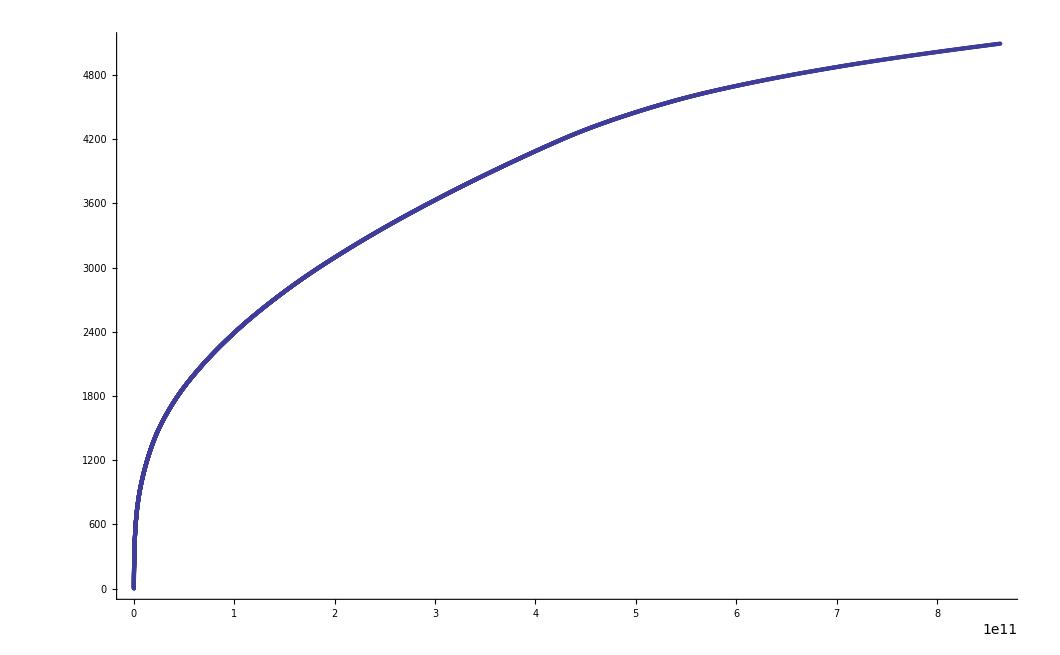

```mathematica
ListPlot[Table[{kl[[k]],k},{k,1,Length[kl]}]]
```

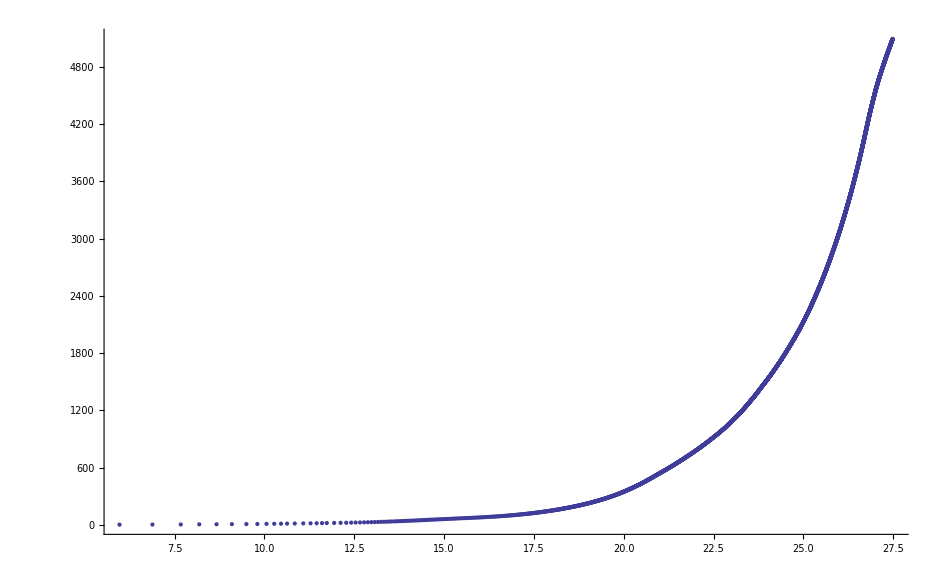

```mathematica
ListPlot[Table[{Log[kl[[k]] ],k},{k,1,Length[kl]}]]
```

```mathematica
With[{p=3,q=5},
Table[
BinRatio[p,q,i,j,1000000000000]
,{i,0,p-1},{j,0,q-1}
]
]
```

{{{61275,65100,95655,174450,183780,241350,641085,678585,794205,831705,947325,984825,1100445,1137945,1216215,1253565,1494195,1522395,1647330,1800465,1828590,1866090,1981710,2019210,2134830,2172330,2287950,2325450,2441070,2478570,2594190,2631690,2688060,2775540,2791065,2944200,3081735,3097335,3875610,4053240,4140720,4313010,5047155,5572215,5762640,6109380,6490890,6568830,7028280,7415925,7487730,7947180,8465775,8734680,9271950,9907335,12813750,13062990,14001270,15110085,15188775,16376295,17157195,17563815,19328805,21375915,22687980,24813780,25922640,26001300,27188820,28829280,30016815,32312955,33376005,37594725,39641820,40829325,41937945,42016845,42797475,44250345,44548035,51219645,51375345,51673035,55531335,55610010,55844190,59328990,59484690,59782380,60922335,61375725,65469195,68187510,68266185,68719065,68797740,70547340,71000730,78344055,78422730,82375080,83515665,84421935,84719220,85031310,85406415,85921890,85937580,86000565,86453445,86532120,86546955,87453225,88593810,89031765,89110440,89422125,90859665,91157355,91235265,91390965,91688655,92000085,93140670,94046940,94656315,95562585,95782245,96171960,96625140,97078230,97453500,97751190,98218815,99344655,99500355,99798045,103891590,104734485,105562890,105860580,107078490,107376180,107454045,107609745,107907435,108218835,109359420,110265690,110781600,110860275,114125430,114578820,115421955,116328225,117468810,120953160,127468830,128609415,129062505,129515685,130125060,131031330,131640705,132546975,133687560,137093835,138234420,138453450,138906840,139140690,139750065,140656335,141265710,142171980,142687770,142766445,143312565,146562795,147016185,147703380,148609650,148907340,149219025,150125295,150578685,150656640,150954330,151265880,152547795,152703495,153001185,153687810,153985500,158688030,159375225,164968800,165047475,173313390,173469090,173766780,174984735,175282425,176500380,176798070,178391535,178547235,178844925,180515910,180969300,181656495,182562765,182860455,182938395,183094095,183391785,183703245,184609740,184907430,186125385,186423075,187328670,187407345,187719030,188016540,188172240,188469930,188625300,189078690,189765885,190672155,190969845,191812590,192953175,193328265,193843770,193859445,193922445,194375325,194454000,194468820,195375090,196515675,196953660,197032335,197344020,198250290,198469230,198547905,198703680,198859590,198922035,199000710,199390875,200297145,200594835,202797240,203250630,204625020,205063050,205141725,205453410,206359680,206813070,207031470,207110145,207500265,213860265,214015965,214313655,214703130,216515955,216813645,222718755,222797430,222876105,223187790,224094060,224547450,225234645,226375005,228563265,228718965,229016655,238937520,239016195,239250495,239469075,239547750,239937690,244031370,246338355,249070755,253916820,256649100,259149420,261649755,266805135,277038435,294463485,299541465,304696845,313359405,314775525,317507805,318451995,319930905,325086240,332741865,342588615,345320895,353906745,358999335,362823270,365555550},{13665,36465,37695,38910,40140,71445,102120,566655,604155,719775,757275,772710,872895,901245,910395,1026015,1063515,1078875,1179135,1207410,1216635,1332255,1369755,1441635,1513590,1594770,1675950,1747905,1819785,1857285,1972905,1982130,2010405,2126025,2163525,2279145,2288295,2316645,2416830,2432265,2469765,2585385,2594460,2622885,2722995,2744865,2878770,2907225,3051060,3475845,3782010,3910545,4088175,4131915,4160370,4304205,4466565,4641525,4797960,4941285,5257410,5400735,5519940,5860185,6319635,6779085,6982020,7441470,7900920,8366400,8825850,9285300,9744750,246904515,248620380,253621035,254481705,256353315,257061570,276665430,284953050,291590085,296822790,301900830,302606445,305186310,306901485,309633765,312056865,327136155,332291535,334791930,337524210,342370215,345102495,347525595,355026585,357758865,373544070,375261240,376123935},{28485,407595,426600,495075,536175,573675,689295,726795,842415,995535,1148655,1301775,1417500,1476780,1629915,1723695,1783050,1876800,1914300,2029920,2067420,2183040,2336160,2489280,2642400,2773650,2926785,2976840,3079920,3217425,3254925,3370545,3408045,3523665,3561165,3676785,3829905,3983025,4223655,4229985,4376790,4529925,4536180,5504970,6423645,7020585,7939260,8142495,8333010,8792460,8864295,49446375,49899765,53164920,53243595,56117760,56415450,56571150,56649015,56946705,58164615,58462305,60133605,64227150,64524840,64680540,66274005,66571695,68242950,72336540,72634230,72789930,72867840,73165530,74603070,74914755,74993430,77493075,77571750,78024630,79305975,85602465,85681140,93024465,93477855,95227455,95306130,95759010,98556000,102649470,103102860,104242815,104540505,104696205,108181005,108415185,112352160,112649850,112805550,119477160,119774850,123415185,123868575,128493210,128946600,133040205,133493595,139180425,139478115,139789800,139868475,141305445,141384120,142821090,142899765,144258570,144711960,147289800,147587490,147899175,147977850,148805430,149103120,149414805,149493480,150930450,151009125,152446095,152524770,153883575,153961710,154040385,154336965,155399190,156008565,156087240,163586700,163665375,164117970,164196645,165024180,165321870,165633555,165712230,168586605,168884295,169039995,171696090,171774765,173133570,173586960,174040350,179649630,180103020,182149740,187758975,188212365,190259130,193524360,193603035,205571010,205868700,206024400,209884335,210196020,210274695,210868680,211555875,212009265,212915535,213149205,213227220,213524910,214431180,214742865,215040555,215946825,216634020,217087410,220493685,221180880,221634270,222540540,222852225,223149915,223914930,223993605,224056185,224212230,224367870,224446485,224665560,225571830,226259025,226712415,226946115,227024790,232024320,232102995,232321575,232555875,242555415,242853105,243008805,245193630,250039665,252771945,255195045,257927325,265428285,268006005,273161385,285585720,288318000,290741100,295664415,298474035,321054480,323786760,336211110,341366490,343944225,351677160,361678590,366911175,369411525,384413550,389489520,392853495,397931820,398234460,403010145,403312785,405667080,405969720,409096815,409331190,411283560,418480365,418783005,420901485,421204125,428400930,428703570,430822050,438321495,442456995,444409365,444643740,445585320,450663645,455741970,458634555,462299940,462534315,464486685,471683490,471986130,474104610,474407250,481604055,481906695,484025175,490581930,492534300,492768675,496131510,499024185,504102510,509652165,509954805,511130670,518630115,521051235,528550680,530503050,530737425,530971800,532924170,540423615,541363755,546677685,551756010,556834335,562619640,562922280,564333795,571833240,574254360,581753805,583706175,583940550,584174925,586127295,593626740,594331230,596283600,599409510,601361880,604018830,604253205,604487835,606440205,609566160,611518530,615587115,617536920,625036365,627457485,634956930,636909300,637143675,637378050,639330420,646829865,649251075,653791065,658869390,659172030,660819360,665426235,674339745,674642385,676760865,677063505,684260310,684562950,686681430,694180875,699023340,701208900,702924660,703159035,706287225,711365550,713551170,718159320,718393695,720346065,727542870,727845510,729963990,730266630,737463435,737766075,739884555,747384000,751990815,753940725,755893095,759019050,760971420,764097375,766049745,766284270,766518645,768471015,771362445,771596820,773549190,780745995,781048635,783167115,783469755,790666560,790969200,793087680,800587125,804958290,808322280,813400605,813703245,818478930,818781570,821135850,821438490,824565570,824799945,826752315,833949120,834251760,836370240,836672880,843869685,844172325,846290805},{3090,5595,14595,119775,142260,4967955,5111280,5427405,5892885,6352335,6495660,6811785,7014720,7474170,7933620,8076945,8393070,8536395,8995845,9455295,10196940,10275615,10308420,11528070,11915865,11948670,11994450,12027255,12105930,12197685,12230490,12715590,13181970,13214775,13293450,14743770,14822445,14855250,15104325,15137130,15931290,16009965,16042770,16731105,17918625,18010965,19526535,21540840,21573645,21822660,21855465,21934140,23121660,23213730,24932820,26356110,26776410,27543630,29072625,29105430,29184105,29650245,29683050,29932065,29964870,30260145,30292950,30371625,31821945,31900620,31933425,32621760,32838705,32871510,33009465,33088140,33120945,33809280,34793580,35541840,35574645,35981100,37496715,38087670,38120475,38619195,38652000,38901015,38933820,39012330,40199850,40948125,41322330,41355135,41446950,41525625,41558430,41604150,41636955,42246765,42634470,42713145,42745950,47854920,48697815,48853515,57165915,57244590,57323265,57776145,57854820,58088760,58542150,59291730,59370405,62557965,62713665,63011355,64916490,65072190,67401135,67479810,68478960,68634660,70291770,70589460,72791760,73245150,74166150,74619540,74900295,74978970,75057645,75510525,75589200,80292345,80448045,80745735,81494085,81572760,81651435,83854785,84010485,84308175,86510580,86808270,88401735,88557435,88855125,89244555,89400255,91291410,96135570,96433260,97807185,98026725,98182425,98323095,98401770,98480115,98635485,99088875,99776070,100682340,100980030,101291715,102197985,102495675,102807360,103713630,104167020,104244960,104542650,104854215,106136115,106291815,106589505,106900905,107588100,108041490,108260490,108713880,108947760,109401075,109463670,109542345,109932210,110307345,110605035,110619405,110916720,111822990,112120680,112432365,113338635,113792025,114104025,114479220,114915840,114994515,115010295,115073190,115151865,115463550,115697490,116150880,117057150,117494385,117573060,117651735,118041555,118728750,122213415,123119685,123806880,124260270,128417385,129260280,129415980,133119915,133417605,134104230,134557620,135244815,136151085,136448775,136526730,136682430,136980120,137291595,137978790,138198075,138495765,140089230,140244930,140542620,141010110,142978965,148198575,148354275,148651965,154728615,155182005,160635330,161151240,161229915,161322315,161775705,162837960,163291350,166853850,170947320,171400710,172526595,172682295,172979985,176478855,177743985,177822660,177901335,177980010,178291695,179197980,179651370,179729235,180026925,180338565,180572325,181025715,181244835,181542525,183213825,183901020,184588215,185853390,185932065,186010740,186089415,186103860,186401100,187307370,187760760,188447955,189354225,189651915,191323170,192010365,192697560,193962780,194041455,194120130,194198805,194510490,195416760,195870150,195948060,196245750,196557345,197166435,197322135,199213290,202386195,203229090,203384790,205275825,205431525,206416065,206869455,207150375,207229050,207307725,207322680,209447385,209900775,214900815,215056515,216104685,216260385,216558075,216947670,217400970,217759530,217838205,217916880,217932090,217995555,218087790,218307240,218916615,219275175,219353850,219432525,219511200,219822885,220432260,220869495,220948170,221026845,221338530,221636220,222479115,222634815,223010205,223165905,223463475,223979385,224058060,224353305,224431980,224510655,224589330,224901015,225729690,225885390,226183080,227025975,227323035,227384535,227463210,227541885,227620560,227776425,227915925,227932245,227994600,228073275,228526155,228541620,228604830,228697425,228978855,229057530,229136205,229150815,229447890,230057265,230573175,230651850,230963535,231261225,232104120,232259820,235432380,235885770,236025315,236103990,236182665,236635545,236714220,236806770,237260160,240572130,240650805,240729480,240808155,241119840,242557380,242855070,256612695,256691625,256924860,261531360,261769815,269347875,279659895,282004065,284815275,294893955,297316740,300049335,302078700,304894965,305049990,309972990,322471995,327629115,332940315,335363415,338095695,340285365,340518705,343096350,348019740,350752020,368017920,373016355},{14610,29925,31155,32385,409020,518355,5099385,5493195,7336905,7802505,8261940,10591395,10623945,10670070,10702875,11778915,11857590,11890395,12435105,13622625,13701300,13734105,13983120,14810145,14888820,14921625,15997665,16030230,16076340,16109145,17920020,17952825,18201840,20248935,22545225,22578030,23122770,23155575,23732745,23765550,24966450,25045125,25077930,25497885,25530690,25779705,26153970,26232645,26265450,27623385,27656190,28030320,28889865,29185200,29263875,29296680,30372720,30451395,30484200,30904170,30936975,31185990,31921020,32170230,32203035,33357750,33390555,33935325,33968130,34794855,34827660,34919550,34998225,35031030,35076675,36107070,36185745,36218550,37747545,37983315,38935065,39794475,40981995,41545995,42169515,42248190,42280995,42904260,42937065,45764775,46062465,46218165,47046870,47358555,47437230,48342780,48640470,48796035,49093725,49327110,49405410,49484085,49624800,49780500,49999995,51373965,51671655,52889610,53187300,53874120,54171810,54327510,54405255,54702945,54858645,55467945,55546620,56905425,57203115,57358815,57812205,58952115,59249805,59405505,60998970,61296660,62514615,62812305,64030260,64327950,64483650,65921595,66296835,66608520,66687195,72218025,72296700,75546585,79640145,80093535,83655975,90327375,101390355,112765005,112843680,115406205,116093400,117311775,117390450,117843330,120874440,120953115,121702560,122155950,122389980,122468655,123515550,124202745,125421165,125499840,125952720,127234095,128983875,131327565,131780955,134436585,134734275,134889975,136859100,145655445,145734120,147092925,147390615,147546315,155811735,155890410,157468650,158155845,158609235,159515505,159827190,159905865,160202610,160656000,164374080,164671770,165578040,166265235,166718625,167015625,167624895,167858520,167936580,168015255,168156210,168311955,168467895,168546570,168765345,169062480,169671855,169983540,170062215,170578125,171187500,171499185,171577860,172483470,172781160,172936665,173234355,173390055,173687430,174374625,174828015,177483525,177781215,178092900,178171575,178687485,178999185,179296860,179608545,179687220,181124190,181202865,182561670,182859360,183015060,185218125,185296800,187108530,187406220,187717905,187796580,188312490,188921865,189233550,189312225,190671030,190968720,191124420,198780375,199078065,199233765,201578100,201889785,201968460,202421055,202499730,214921380,215374770,217577220,217874910,218781180,219171390,219468375,219921765,224546400,224999790,230233365,230531055,235233630,239546775,240233970,240687360,241593630,241905315,242203005,243109275,243342975,243420960,243718650,254447475,255609525,259602855,260702115,262257900,269681535,272413815,274836915,279760275,282492555,287647875,296156865,299994930,302727210,330385650,343196610,345619710,348351990,350852340,353352645,360930975,363354075,366086355,371087010,389137125,389439765,391558245,391860885,399057690,399360330,401478810,401781450,406792635,407095275,414527880,414830520,419606205,419908845,426398790,432419685,432722325,434840805,435143445,442340250,442642890,444761370,445064010,452260815,452563455,454681935,454984575,459760110,460062750,467259705,471396660,471631035,472338030,472640670,479366265,481318635,483975150,484209525,485622810,485925450,488043930,488346570,489053175,489287550,494131200,494365575,495543375,495846015,497964495,498267135,499209225,499443600,504287250,504521625,505463940,505766580,507885060,508187700,509365275,509599650,512727585,519991530,525069855,533983470,534286110,538825935,539128575,541247055,541549695,548746500,549049140,551167620,551470260,558667065,558969705,560852520,562568385,562802760,565459395,567109125,567411765,574137420,574440060,575146995,575381370,578980050,579282690,586479585,586782225,588900705,589203345,596400150,598821270,606320715,608741835,617419695,617722335,621790920,626869245,627171885,631947525,632250165,639682710,639985350,642103830,642406470,649603275,652024395,659523840,661944960,670387170,670689810,674522745,679601070,684915000,692885835,693188475,695306955,695609595,702806400,705227520,712726965,715148085,723354645,723657285,727255965,727490340,728904300,729206940,735225570,737177940,740775150,743903310,744205950,751402755,751705395,753823875,754126515,761323320,761625960,763744440,764047080,769293930,769596570,777264840,777567480,782343165,782645805,788900085,794685315,794987955,797106435,797409075,804605880,804908520,807027000,807329640,814526445,814829085,816947565,817250205,822261405,822564045,829996665,830299305,835074990,835377630,841867560}},{{4943940,5121930,5403390,5862840,6322290,6781740,6978615,7247220,7706670,8166120,8369055,8828505,9019185,9287955,9431280,10500075,10532880,10611555,12015690,12048495,12127170,12422430,12455235,13203210,13236015,13314690,15125565,15158370,16437645,16470450,16549125,17736645,18032205,18924165,19265640,19298445,20453160,20485965,20938845,21187860,21220665,21640680,21673485,21752160,22657770,22782435,23031450,23064255,23845290,24750540,24783345,24875130,24907935,24986610,26141610,26876520,28064040,28188720,28437735,28470540,28890645,28923450,29704290,29953305,29986110,30078165,30110970,31265685,31298490,31377165,32859945,32892750,34126485,35766585,38797740,39657285,40549185,42156915,46955310,47939610,48393000,49080195,49986465,50970900,51424290,52345290,52798680,55142730,56049000,56502390,57189585,58095855,58549140,59080245,59533635,60220830,61127100,61736475,62642745,63096135,63110475,63408165,63783330,64314435,64767720,65001630,65455020,65673990,66127380,66814575,67720845,71205480,71892675,72877110,73783380,74236770,74470725,74782410,74861085,74923965,74939760,75235365,75533055,75688755,75908265,77282220,77579910,83344755,83642445,83798145,85080030,85391610,85689300,85767225,86220615,87126885,87438570,87736260,88642530,88954215,89251905,90158175,90845370,91298760,91454145,91751835,91907535,92127090,93564630,94705035,95392230,95845620,96220695,96751890,96907890,97063575,97142235,97220910,97361265,98267535,98579220,98876910,99783180,100470375,100923765,104330040,105017235,105470625,106376895,106596525,106688580,106986270,107141730,107439420,107595120,107892540,108267840,108579735,109033125,110158995,110314695,114876615,114955290,115314690,115768080,116689080,117142470,119344815,119642505,121080045,121391730,121470405,126377715,126533415,130924590,131080290,136547895,136845585,137001285,141080715,141236415,142079310,148736640,151767945,152455140,153142335,154892160,154970835,156846030,157313490,157611180,157766880,159360345,159658035,159877290,160564485,160875990,161173680,161251680,162391635,162689325,162845025,164955420,165408810,165564510,165954135,166251825,166407405,166705095,166938495,167236185,167391885,167611365,168985350,169283040,170500995,170798685,171485520,171783210,171938910,172016640,172314330,172470030,172767630,173079315,173157990,173236665,173673900,174516795,174814485,175720755,179127330,179814525,180798990,181705260,182158650,182392620,182704305,182782980,182845845,182861655,183298890,184141785,184439475,185345745,186188520,186486210,186641910,190502010,190813695,190892370,190971045,191408280,192251175,192548865,192704565,193157955,195877155,196330545,197251545,197704935,201267345,202470855,202924245,203611440,203986500,204439890,204517710,205127085,205360890,205814280,206033355,206642730,207549000,208002390,208689585,209376735,212095860,212549250,213236445,214142715,214752090,215049525,215205225,215658360,216048120,216267735,217174005,217627395,217720305,217798980,218314590,221720865,222174255,222861450,223767720,224377095,225283365,225736755,225829710,225892740,225908385,226423950,226799010,227252400,227939595,228782280,229079970,233846100,233939100,234017775,234533295,238846470,239002170,248134980,250867260,271179345,271966920,281180715,298837755,303838380,311416845,312500340,314149125,319149780,324305160,335327340,367120245,369852525,394069530,397432455,397666830,397969470,399619200,405873405,406176045,411961200,414382320,421881765,424302885,431499690,431802330,434694825,435401010,435635385,440008740,445087065,448515660,450165390,453998340,454300980,457664880,465164325,467585445,475084890,477506010,484702815,485005455,487662300,488604135,488838510,492740565,497818890,502897215,506965815,507268455,510868005,511339035,511573410,516417060,516651435,518367450,520788570,521495085,521729460,526573110,526807485,528288015,530709135,531651135,531885510,536729160,536963535,537905940,538208580,540327135,540629775,541807260,542041635,545169750,545472390,550248075,550550715,551963685,552198060,555326400,555629040,559933290,560235930,561885660,564071130,571570575,573991695,581491140,583912260,588452070,588754710,595715940,596018580,600625545,602275275,609539235,612667200,612901575,614381775,616802895,617745225,617979600,622823250,623057625,623999700,624302340,626420820,626723460,627901275,628135650,632979300,633213675,633920265,634222905,636341385,636644025,638057325,638291700,640948185,641250825,642900555,649928775,650635785,650870160,655007100,662506710,667584900,670006020,677202825,677505465,679623945,679926585,687123390,687426030,689544510,689847150,695868030,702357960,702660600,707436285,707738925,715171545,715474185,720788025,723209145,730405950,730708590,732827070,733129710,740326515,740629155,742747635,743050275,748835505,755089785,755392425,760168110,760470750,768139020,768441660,773991150,776412270,783609075,783911715,786030195,786332835,793529640,793832280,796960440,800557650,800860290,802510020,808528650,808831290,810245250,810479625,814380945,820937775,822587505,825008625,832508070,834929190,842428635,844849755},{585,1170,4410,6030,54585,380130,501075,803835,1022535,2056980,2494380,3310125,3616320,3660060,4563270,4838520,5297970,5560515,5703840,6019965,6163290,6622740,6885285,7344735,7804185,8263635,8406960,8723085,8866410,9266325,9325860,10488780,10521585,10567350,10770600,11754870,12614280,13801800,14051460,14084265,14333280,15691710,15724350,15770385,16833030,17410635,17443440,17692455,18020550,19287030,20192355,21301335,21334140,21379875,21583155,22160865,22193670,22442685,23020350,24207870,24489795,25349325,27363630,27442305,28052460,28629825,29817345,30066765,30145440,30598290,30631095,30880110,31332960,31582380,31661055,32848575,33458745,34036095,36161880,37021410,37270530,38458050,39035715,39068520,39317535,39895245,39928050,40019850,40098525,40177065,41207370,41286045,42224175,45849645,49255770,54256140,55927485,56006160,60474375,62365530,62974275,63427665,64036875,64115550,65021130,66005595,66458985,70099365,71990520,73661865,73740540,75021795,78208755,79271400,80099910,85255635,85709025,93364980,93818370,104428005,108677790,119131005,125349450,125428125,125880720,129818235,135349725,135803115,137927580,138536955,139365585,140052600,141490080,141943470,142631055,146036940,146646315,146724990,148161960,149599425,149677605,150052815,151115085,151568475,153693030,155661945,156271320,156349995,157786965,159302610,159833925,160740090,161193480,167943315,169911855,170896155,171349545,171958770,172037445,172943010,173927445,174380835,179005545,179458935,181052400,181505685,182036790,182115060,182193735,182490180,184083645,185599290,186052680,188630535,189083925,190677390,194162025,196739925,197193315,198865305,201896460,202428015,205459200,206974740,210005850,210537405,215084175,216521175,229553070,231224385,233115540,238271235,238724625,249238185,254316375,259236000,269706450,272361465,274707105,279469665,279785130,282285240,282517410,284940510,289706115,292596120,294704775,297751470,312439170,317908815,320016900,320331915,323064195,325409880,328064850,333065565,337751310,350566260,355485720,365721915,370800255,373689690,375799245,378535320,380797680},{390,87195,104700,114015,117840,135930,154065,184740,532845,676680,839040,970260,1276425,1404960,1582590,1711125,1929825,2092185,2236020,2345385,2382885,2463975,2498505,2536005,2651625,2689125,2770140,2804745,2842245,2898675,2957865,2995365,3076305,3110985,3148485,3285990,3295005,3323460,3439125,3467295,3592260,3629655,3673395,3751635,3789135,3904755,3942255,3979560,4057875,4095375,4108095,4210995,4248495,4285725,4364115,4401615,4414260,4517235,4554735,4698570,5179590,5501745,5645070,5961195,6104520,6563970,7023420,7482870,7942320,8085645,8401770,8545095,8861220,9004545,9463995,9726540,10022415,10101090,10133895,10600275,10711140,11209935,11288610,11321415,11787795,12397440,12476115,12508920,12758235,12975300,13663635,13696440,14162820,14772540,14805345,14851155,14883960,15225435,15632070,15664875,15913890,15946695,16412955,17600475,17679150,17711955,18007185,18039990,18289005,18321810,18912855,20100375,20336115,20539620,20881455,21491115,21569790,21602595,23131605,23413470,23446275,23695290,23728095,24319125,24850440,26037960,26444625,26477430,26726445,26759250,27225480,27304155,27336960,27585975,29633085,30053475,30492615,30741810,30774615,31929330,31962135,32506920,32539725,32788740,32821545,34022490,34055295,35695380,35866170,35944845,35977650,36444030,37007490,37040295,37414470,39428775,39461580,39678480,40366815,40399620,41305170,41554335,41587140,42506475,44116485,44414175,44569875,47678955,47976645,48132345,49789455,52289445,52742835,53663835,54117225,59790030,59945730,63352470,63508170,64351065,66008265,67899420,68055120,68444550,68742240,68897940,70491405,70789095,75633255,77304870,77524410,77680110,78133170,78586560,79273755,80180025,80789400,81695670,82305045,83211315,83664705,83742645,84351900,85633800,85789500,86398590,87085785,87539175,87758175,88211565,88445445,88898760,89429895,89805030,90117090,90414405,91320675,91930050,92836320,93289710,93304020,93601710,93976905,94507980,94961235,95195175,95648565,96554835,97539240,98226435,101413410,101711100,102617370,103304565,103757955,107915070,108460275,108757965,108913665,112617600,113601915,114055305,114742500,115648770,116024415,116180115,116789280,117476475,117695760,119586915,119742615,120507795,122178960,122476650,127696260,127851960,134226300,134679690,140133015,140820000,141273390,142335645,142789035,146351535,150445005,150898395,152024280,152179980,153022875,155976540,157789380,158695665,159149055,159226920,159836250,160070010,160523400,160742520,162711510,163398705,164085900,165601545,165898785,166805055,167258445,167945640,168851910,170820855,171508050,172195245,174008175,174914445,175367835,175445745,176055030,176366430,176664120,176819820,178413285,178710975,181883880,182429085,182726775,182882475,184475820,184773510,184929210,185913750,186367140,186522675,186820365,188945070,189398460,194100810,194398500,194554200,195602370,195758070,196055760,196147665,196445355,196600965,196898655,197132085,197429775,197585475,197804925,198414300,199320570,199929945,200836215,201133905,201679110,201976800,202132500,202210200,202507890,202663590,202961160,204398700,205227375,205383075,205680765,206225970,206523660,206820720,207274110,207429930,208039305,208195110,208648500,208945575,209554950,210461220,210758910,211304115,211601805,211757505,214930065,215383455,216304455,216757845,220617525,222055065,225993090,226148790,226991685,231071115,231226815,231524505,232069710,232367400,233273670,235618110,235773810,241758330,250970010,264488685,281991060,284723340,297225045,302225715,304957995,307303725,310036005,312459105,315191385,324406470,325270065,330425445,343081755,352928475,368162505,370740165,373163160,375895440,383473905},{2220,15465,31740,4858680,5002005,5461455,5920905,6380355,6839805,6983130,7299255,7442580,7758705,7902030,8421090,8564415,8880540,9023865,9339990,9483315,9792870,10370115,10402920,11400600,11964480,12588120,13775640,14011590,14963160,15041835,15074640,15323655,15619350,16806870,17370765,18119265,18558315,18807600,18840405,19306785,19995120,20027925,21432150,21464955,21556920,21635595,21668400,21713970,21746775,22744440,22823115,22855920,23557650,23590455,24666810,24699615,24745170,24777975,24948630,26011680,26588880,26621685,27776400,27809205,28025985,28058790,28307805,28340610,28963920,28996725,30230400,31181925,31260600,31293405,32244705,32277510,32369445,32448120,32480925,32526525,32559330,33556950,33635625,33668430,34291800,34324605,34573620,34744470,34823145,34855950,36384945,37480260,37572465,39855375,41463105,42355005,46853655,48900510,49042080,49197780,49495470,50557755,50713425,51011115,51400650,51556350,52604580,52760280,53057970,56244585,56697975,57385170,58291440,58589130,58900815,59807085,60104775,60416460,60713925,60869625,61167315,61322730,61776120,62463315,64353960,64807350,65494545,65869590,66322980,66400815,66698505,67010175,67243965,67697355,67916445,68214135,68525820,69432090,69729780,70041465,70947735,71088045,71166720,71245395,71401125,71540895,71557080,71619570,71698245,72088320,72463350,72916740,73603935,74510205,74807895,75353310,75806700,79369200,80713035,80791710,80870385,81182070,82088340,82541730,82619610,82917300,83228925,83462670,83916060,84135195,84432885,86104155,86791350,87478545,88822425,88901100,88979775,88994205,89291460,90197730,90651120,91338315,91947405,93087675,93541065,93821925,93900600,93979275,93994260,97167180,98010075,98165775,98619210,100056795,102103650,105276525,106119420,106275120,108166185,113071905,113150580,113229255,113603460,113682135,113760810,115510365,115963755,118931415,119384805,121181295,121259970,121338645,123088560,123775755,127322355,127401030,127479705,127791390,128620035,128775735,129073425,129916320,130213365,130353555,130432230,130510905,130666755,130806285,130822590,130884960,130963635,131337840,131416515,131431965,131495190,131587755,131869200,131947875,132026550,132041145,132338235,132947610,133384845,133463520,133542195,133853880,134151570,134994465,135150165,138245040,138400740,138698430,139541325,139978560,140057235,140135910,140447595,141056970,141276390,141432090,141494205,141572880,141651555,141729780,141963240,142572615,143009850,143088525,143167200,143478885,143776575,144619470,144775170,145447755,145745445,149385735,149541435,149839125,155526000,156650070,156728745,156807420,160072965,160760160,163635390,164088780,164244480,164542170,165385065,165822300,165900975,165979650,166291335,172963170,173260380,173400405,173479080,173557755,174775995,175463160,176150355,179854140,180307530,181369770,181823160,181978860,182276550,183119445,183556680,183635355,183714030,184025715,184401000,185838990,186681885,189181980,189479145,189619215,189697890,189776565,189932535,190088250,190150500,190229175,190307850,190385940,190619535,191228835,191666070,191744745,191823420,192135105,193948335,194104035,194401725,195619680,195917370,195995160,196150860,196448550,197510835,197666535,197964225,198806970,199244205,199322880,199401555,199713240,200010930,200853825,201291060,201306885,201369735,201448410,201760095,201994080,202447470,203353740,203963115,204869385,205478760,205620180,205775880,206073570,206385030,206822160,206900835,206916360,206979510,207072225,207353595,207432270,207510945,207525615,207822630,208120320,208963215,209118915,209572305,209853240,209931915,210010590,210931890,211619085,212072475,212150220,212603610,212978745,213588120,214494390,215103765,216010035,216697230,217150620,217681695,217962675,218041350,218120025,218134950,220259565,220712955,225791085,226072110,226150785,226229460,229948200,230103900,230401590,235791315,236228550,236307225,236385900,236775630,237462825,237916215,238057545,238213245,238510935,238822485,239259720,239338395,239353830,239417070,239509605,239791065,239869740,239948415,239962995,240260100,240869475,241306710,241385385,241464060,241775745,242073435,242916330,243072030,249040650,254196030,255295215,256851090,265452270,278094075,294742785,314977440,319978110,325133490,335212170,336389925,337944450,340367550,363102570,365834850},{5235,9870,312435,334260,402810,421815,552510,580965,652875,724800,806010,887160,930900,943515,981015,1096635,1134135,1237065,1249755,1287255,1365600,1402875,1440375,1543230,1555995,1593495,1671765,1709115,1746615,1834110,1949745,1977945,2102880,2140305,2256015,2284140,2321640,2402745,2437260,2474760,2590380,2627880,2708910,2743500,2781000,2837445,2896620,2934120,3015075,3049740,3087240,3143610,3231090,3246615,3393450,3399750,3537285,3552885,3896460,4024995,4202625,4331160,4508790,4596270,4624725,4768560,4793670,4936995,5253120,5396445,5855895,6315345,6774795,7234245,7377570,7693695,7837020,8618625,8761950,9078075,9221400,9680850,10263735,10512930,11372460,13419570,14279100,17310255,20669430,22716540,25091655,26154390,27341910,28247310,28529430,30294405,34513125,35576175,37872300,39059850,41966490,42169935,43668825,43747500,44810145,47997105,49278360,49357035,51028380,52919535,56559915,57013305,57700080,57997770,58903350,58982025,59591235,59746935,60044625,60653370,62544525,67012740,67091415,68762760,73763130,77169255,80356830,80512530,80810220,81872475,82028175,82325865,83543820,83841510,85434975,85590675,85888365,89981835,90137535,90435225,91340895,91653180,91793775,91872450,91950870,92106315,92559705,93168825,93466515,95059980,95215680,95513370,99606840,99762540,100060230,101278185,101575875,102793830,103091520,103169340,103325040,103622730,104684985,104840685,105138375,106496970,106575645,111278685,111434385,111732075,115903260,123247065,123325740,124012650,125450580,125606280,125903970,128481900,133637640,136668915,139997400,141747030,142200420,142653810,144012615,144091290,147731940,150075150,150153825,150763200,152122005,152200680,155841285,158184540,158263215,158872590,166075125,166528515,169325115,169403790,174934620,175013295,176684640,181231515,191841150,192294540,197450235,199341390,201012705,213746910,214044600,215481600,220028370,220559925,223591035,225106575,228137760,228590640,228669315,231700470,233372460,233528160,233825850,236403750,239590695,239888385,241481850,241637550,241935240,244294350,249372690,259608885,264528345,277343295,282029040,287029755,289684725,294762690,295077705,297185790,302655435,320389830,322498485,325388490,330154095,332809365,335309475,335624940,340387500,342733140,345388155,355858605,360778230,365856420,373434480,386090670}},{{4770,6390,15270,55095,56325,365070,406725,431460,475200,494205,594270,609705,647205,762825,771900,800325,900435,922305,1084665,1228500,1653285,1781820,1959450,2087985,2337810,2481645,2644005,2818965,2947500,3125130,3253665,3431295,3559830,3734790,3897150,4040985,4290810,4419345,4596975,4725510,4859805,4919265,5378715,5844195,6303645,6375420,6763095,7300455,8028675,8225490,8284770,8744220,9144165,9203670,10470690,11219175,11907510,11940315,12406695,12845805,13095030,13127835,15437925,16126260,16159065,16204980,16625445,17313780,17346585,17845095,17877900,19236135,20594415,20673090,20705895,21172275,21860610,21893415,22142775,22359795,23048130,23080935,23422410,24609930,25016610,25049415,25298430,25331235,25797450,25876125,25908930,26532180,26564985,26656860,26735535,26768340,26814000,26846805,27844380,27923055,27955860,28422240,29812965,30875610,30954285,30987090,31938465,31971270,32063130,32141805,32174610,32220285,32253090,33047415,33782055,33814860,34063875,34096680,34234935,35422455,35501130,35533935,36970515,38250450,38938785,38971590,39877155,40126305,40159110,41484885,42580290,42672405,43219830,44813460,45797925,45953625,49891695,50797965,51485160,51938550,52157535,52610925,52844820,53298120,53829240,54204390,54502080,54516435,54813765,55720035,56017725,56329410,57235680,57689070,58001085,58376265,58907355,58970265,59048940,59360625,59594550,60047940,60798165,61095855,61782540,62235930,62923125,63829395,64127085,64205070,64438770,65047965,65203665,65345040,65642730,65954415,66860685,67314075,68001270,72314415,73157310,73313010,77016990,77314680,82548255,83001645,83922645,84376035,87626280,88079670,88376655,88766865,89673135,89970825,92173275,92626665,94532160,98625645,99079035,104532405,105579585,105658260,105969945,108314280,108469980,108767670,109312875,114844365,115297755,116423625,116579325,116877015,117422220,117719910,118173030,118314495,118626180,118860225,119235555,120141825,120439515,121282410,121438110,124532985,124688685,124986375,125829270,126423855,126735540,127344915,127939500,128251185,128548860,128860560,129391755,129547455,129766830,130064520,130907415,131063115,132720030,133173420,133485360,133860615,134157990,134313690,134611380,134766885,135064575,135454275,136048860,136360545,136969920,137876190,138485565,138782700,139236090,139391835,139611465,139689525,139923150,140532420,140688120,140829420,141282810,141970005,142876275,143173965,146892045,147345435,147642180,147720855,148032540,148938810,149392200,149704185,150079395,150688485,150844185,151141725,152735340,153719775,153875475,158797875,158953575,160001730,160157430,160455120,160844730,161298015,161813925,161829120,161892600,161984820,162204285,163875975,165391620,165547320,168422865,168578565,170469720,170688945,172658070,172813770,173111460,173656665,175767090,176220480,176532255,176687955,178564170,180313950,181595325,183345300,184032495,185392095,185845485,189704715,191454645,192141840,196313505,206157690,208360515,209047710,211016715,211922985,212610180,213063570,217220670,218063565,218219265,223892070,227454510,227907900,228828900,229282290,232001460,232688580,233375775,233829165,234735435,240860850,240939525,241251210,241626450,243064395,243220095,243517785,243531900,243985290,256564515,261564195,264220665,266875815,269220765,277031745,279454845,287110470,297111405,302032125,307345125,334922010,345391575,347657430,352735770,355392585,357734760,363125955,367891425},{63915,94590,225765,229590,563565,869730,957210,1119570,1263405,1291860,1423080,1600710,1729245,2035410,2372715,2516550,2678910,2757135,2788260,2794635,2910255,2916795,2947755,3063375,3094425,3100875,3216495,3222960,3253995,3369615,3407115,3522735,3529125,3560235,3747825,3763365,3910185,3916500,4054020,4069635,4082475,4126215,4163385,4200885,4303845,4316505,4354005,4432380,4469625,4507125,4610010,4622745,4660245,4738545,4775865,4979190,5122515,5438640,5641575,6101025,6560475,6703800,7019925,7163250,7479375,7622700,8082150,8541600,9001050,9460500,10004400,10037205,10831455,10910130,10942935,10956330,11191950,11224755,11644665,11677470,11756145,12832185,12864990,12943665,13239060,14098590,14393985,14472660,14505465,15581505,15660180,15692985,16112895,16145700,16394715,16427520,16506195,17300445,17333250,17582265,17615070,17693715,18881235,19425945,19458750,19537425,20613465,20646270,20692425,20724945,21912465,22706730,22739535,22988550,23021355,23099985,24018990,24097665,24130470,24911145,25206510,25285185,25317990,26394015,26472690,26505495,26925435,26958240,27207255,27240060,27581535,27660210,27693015,28159395,29222010,30113895,30146700,30409530,32489010,34096950,34300170,34706820,34739625,34988640,35021445,35487690,35566365,35599170,35848185,35880990,37895295,38597520,38630325,38847015,38879340,38912145,40034535,40926450,41785980,42021870,43614990,43926675,44224365,45130635,45817830,46271220,49457835,49755525,49911225,51115155,51504690,51802380,51958050,53020335,53318025,53473725,53615295,55662150,60740175,61583070,64239315,64317990,64396665,64833900,66271440,71271705,71958900,76427745,77943390,79381050,79459035,80068245,81505890,82490265,86052750,87568395,89084040,91130895,93645705,93724380,93803055,96676875,96755550,96834225,97208430,97287105,102660945,102958635,103114335,104707800,105005490,105692280,105989970,106145670,106223445,106521135,107739090,108036780,108192480,110005680,110317365,110396040,110474715,110833935,110848635,110927310,111005985,111287325,111380100,111443220,111458775,111537450,111974520,112285950,112583640,112739340,112880790,114332805,114630495,115380915,115834305,115848450,116146140,116755305,117208695,117364095,117442470,117521145,117599820,117661785,117817485,118037055,118943325,119396715,119489535,119568210,120083910,120990180,123490260,123943650,124864650,125318040,125551860,125630535,125709210,126146445,127052715,127067460,127146135,127224810,127506105,127598970,127662045,127677645,128193300,128504700,128802390,128958090,129099585,130551555,130849245,134708985,136614090,136911780,137067480,140255025,140333700,140412375,141083325,141536715,141770625,141849300,141927975,142302180,142380855,147754695,148052385,148208085,149192670,149646060,149801550,149880015,149958690,150037365,150099240,150411570,150490245,151317195,151614885,152832840,153130530,153286230,157379700,157677390,157833090,159037005,159426555,159724245,159879900,160942200,161239890,162457845,162755535,162911235,167146350,167989245,168286935,168598620,168677295,168755970,169193205,169802580,170099685,170114265,170192940,170271615,170553075,170645610,170708850,170724285,170802960,171240195,171551745,171849435,172005135,172146465,172599855,173287050,173676780,173755455,173834130,174271365,179661090,179958780,180114480,183833220,183911895,183990570,184271595,189349725,189803115,191927730,191942655,192021330,192380985,192912060,193365450,194052645,194958915,195568290,196474560,197083935,197459070,197912460,197990205,198443595,199130790,200052090,200130765,200490375,201099465,201942360,202240050,202537065,202551735,202630410,202709085,202990455,203083170,203146320,203161845,203240520,203677650,203989110,204286800,204442500,204583920,205193295,206099565,206708940,207615210,208068600,208302585,208614270,208692945,208755795,208771620,209208855,210051750,210349440,210661125,210739800,210818475,211255710,212098455,212396145,212551845,213614130,213911820,214067520,214145310,214443000,215660955,215958645,216114345,217927575,218239260,218317935,218396610,218833845,219443145,219676740,219754830,219833505,219912180,219974430,220130145,220286115,220364790,220443465,220583535,220880700,223380795,224223690,225661680,226036965,226348650,226427325,226506000,226943235,227786130,228083820,228239520,228692910,229755150,230208540,233912325,234599520,235286685,236504925,236583600,236662275,236802300,237099510,243771345,244083030,246897345,251666010,256821390,269400375,274555755,277288125,284634435,287366715,289789815,294790500,297522780,302600775,303623820,315025155,317757435,326422800,335259810,349249830,358149510,360572610,363304890,365882565,368305545,371037825,375806550,380961930,385962585,417531165,419483535,424561860,427218690,427453065,464951490,475343625,475578000,483077805,483312180,485264550,520575900,536280930,536515305,538467675,589484055,589718430,591670800,627452595,627686970,637374570,677764110,682842435,726124695,726359070,779092170,789484305,789718680,825030630,825265005,827217105},{1440,42210,43440,44655,45885,651270,804390,963765,1116900,1270035,1445040,1598160,1751280,1904400,2057520,2210640,2320005,5379435,5641935,7485645,7820010,9001260,9204390,48319140,48772530,53928225,55819380,57490695,70522590,71959590,76506360,77037915,80069025,81584565,84615750,85147305,88178460,89850450,90303840,92881740,96366375,97959840,98413230,100991085,101444475,102960120,104553585,104850030,104928705,105006975,105538080,105991365,107584830,108038220,112662930,113116320,114100755,115006320,115084995,115694220,116147610,117131910,119100450,125850285,126303675,127209840,127741155,129256800,130693770,130772445,131381820,133350735,135475290,135928680,136990950,137366160,137444340,138803130,138881805,140318775,140397450,141006825,144412710,145100295,145553685,146991165,147678180,148428135,148506810,149116185,151240650,151694040,157225530,161163045,161615640,161694315,167912760,178365975,182615760,193225395,193678785,201334740,201788130,206943855,207772365,208835010,212021970,213303225,213381900,215053245,216944400,220584780,221038170,222022635,222928215,223006890,223616100,224069490,224678235,226569390,231037605,231116280,232787625,237787995,241194120,247074375,261685200,264340275,267072555,269967405,271995945,274573590,276996600,279728880,282151980,285202800,302232000,307310025,310042305,313013595,315042960,317466060,317775555,320198340,327544680,330277020,335432400,340905015,353560935,358167435,373794315,378402090,385825755},{78525,82350,200400,231075,231645,297975,533460,614445,649080,686580,742980,802200,839700,949065,1042830,1092900,1195965,1255260,1349100,1377225,1414725,1473960,1530345,1567845,1602495,1683465,1720965,1780125,1836585,1874085,1908660,1989705,2027205,2086290,2142825,2180325,2214825,2339700,2346045,2492835,2508405,2645970,2652240,2755350,2870970,2908470,2945805,3024090,3061590,3074340,3177210,3214710,3251970,3330330,3367830,3380505,3483450,3520950,3558135,3636570,3761550,3789705,3905385,3942840,4067745,4095975,4133355,4439520,4568055,4745685,4802430,4945755,5405205,5864655,6324105,6783555,7046100,7189425,7505550,7648875,7965000,8108325,8370870,8830320,9289770,9749220,9900225,10588560,10621365,10995315,11028120,11087745,11776080,11808885,12728220,13337880,13416555,13449360,13901955,13915740,14525400,14604075,14636880,15509685,15745545,16087545,16697205,17275065,17759850,17838525,17871330,18337710,19026045,19058850,19728435,20306295,20915955,21151830,21493815,22353225,22667400,22962885,23041560,23074365,23540745,24150405,24229080,24261885,25541235,25574040,25790880,25823055,25855860,26978400,27666735,27699540,28729695,28762500,28854255,28887060,31479030,31511835,31760850,31793655,32712750,33401100,33433905,34838205,34871010,35120025,35152830,37213320,37246125,37291740,37324545,37495140,37527945,38479260,38512065,39542250,40041060,40119735,40152540,40401780,40618920,41228580,41307255,41340060,41806440,42416085,42448875,42494760,42527565,42993945,46309155,49261995,49715385,51308850,53808975,54262365,57371385,57824775,59418240,61918320,62371710,65480775,65934165,67527645,70637310,85793385,97309365,102543480,105418710,108527745,108981135,110574525,111027915,122699655,123309030,127777785,128231175,129371565,130355790,130809045,131340120,131418420,131793510,133386975,134902620,135887130,136340520,136418265,136871655,137480955,138918435,139371825,140965125,141418515,143011980,144527625,146043270,146496660,148621530,154231035,172340385,194778015,199324785,202887450,203715570,204402990,207434175,213340575,216449595,216902985,227668455,229105935,229559325,237824745,241840200,242215620,246466410,248966205,251465955,253810860,256466055,264122205,269122305,271545225,274122960,294434970,302169345,314747355,314825595,319982715,324748350,327403605,329903730,337638105,347483445,350061165,350294355,360294405,362717505,365528895,370295820},{45615,46845,48075,70575,83715,93090,48061890,48515280,50264835,50343510,50796390,57906225,58749120,66015570,66858465,70046370,72687330,73374525,73827915,74734185,75045870,75124545,77234295,77921490,79592760,79890450,80796720,81108345,81406035,81483915,81937305,82843575,83155260,83233935,89217750,89515440,90421710,91108905,91562295,91937325,92327400,92406075,92468565,92624520,92780250,92858925,93077910,93984180,94295865,94593555,95499825,95811510,96109200,97015470,97327140,97624830,97702665,98156055,98531100,99218295,99671685,101562330,102249525,102702915,102858330,103156020,103311720,103609185,103920870,104218560,105124830,105436515,105734205,106640475,107327670,107781060,110967675,111265365,111421065,112624995,113014530,113312220,113467890,114530175,114827865,114983565,123092910,125749155,125827830,126343740,133468740,141578085,155155545,155234220,158186715,158265390,158718270,164170785,164468475,164624175,166217640,166515330,167202120,167499810,167655510,167733285,168030975,169248930,169546620,169702320,171515520,171827205,171905880,172358475,172437150,172889940,172953060,172968615,173484360,173795790,174093480,174249180,175842645,176140335,177358290,177655980,178265145,178718535,178873935,178952310,179030985,179171625,179327325,180999375,181078050,181593750,186374490,186827880,187061700,187140375,188577300,188655975,189108810,189187485,190014540,190312230,190467930,192061395,192359085,198123930,198421620,198577320,201764865,201843540,202593165,203046555,203280465,203359140,203812020,209264535,209562225,209717925,210702510,211155900,211311390,211389855,211468530,211609080,211921410,212827035,213124725,214342680,214640370,214796070,218889540,219187230,219342930,220546845,220936395,221234085,221389740,222452040,222749730,223967685,224265375,224421075,228656190,229499085,229796775,230108460,230187135,230703045,231312420,231624105,231702780,232155450,232218690,232234125,233061585,233359275,233514975,235186620,235265295,235781205,241170930,241468620,241624320,259911345,262643625,266860140,267412335,272567715,280146000,282646395,285378675,287801775,295534710,302881065,304908765,308036445,313037100,315769380,318115140,320847420,323347845,353033505,358584615,361316895,366317550,369049830,371472930,376396305,379128585,381706215,384129240}}}

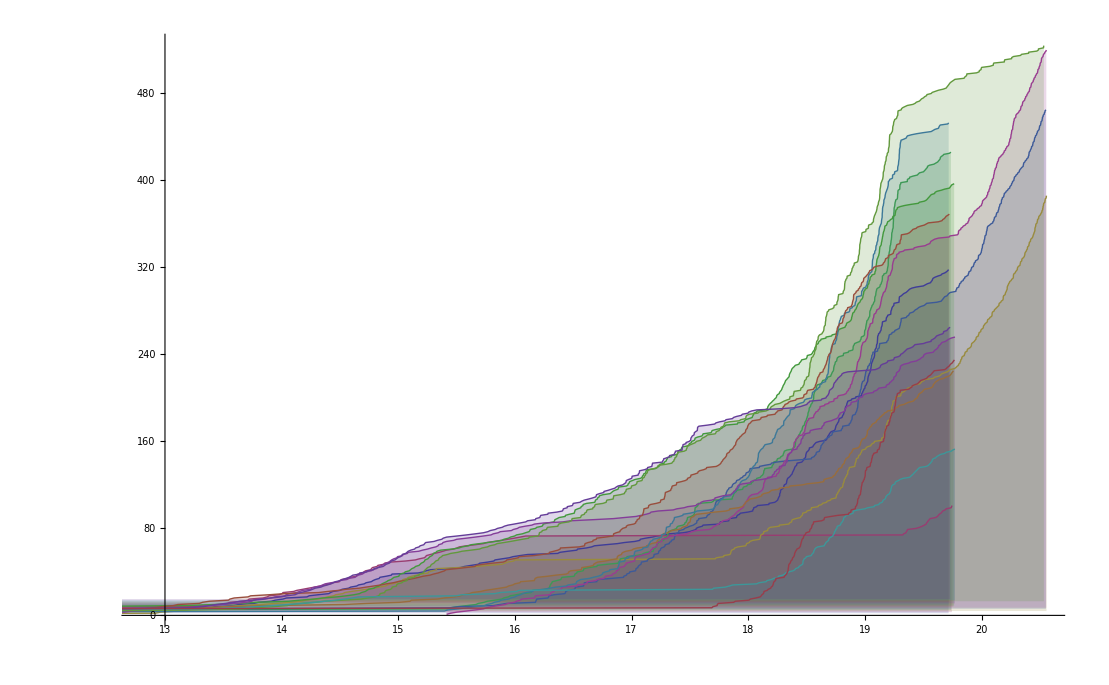

```mathematica
With[{p=3,q=5},
ListPlot[
Flatten[
Table[
With[
{zz=BinRatio[p,q,i,j,1000000000000]},
Table[{Log[zz[[k]] ],k},{k,1,Length[zz]}]
]
,{i,0,p-1},{j,0,q-1}
],
1],
Joined->True,
Filling->Table[{r->r+1},{r,1,p*q-1}]
]
]
```

Filling::invfillentry: 7 → 8 is not a valid Filling specification.

Filling::invfillentry: 9 → 10 is not a valid Filling specification.

Filling::invfillentry: 11 → 12 is not a valid Filling specification.

General::stop: Further output of Filling will be suppressed during this calculation.

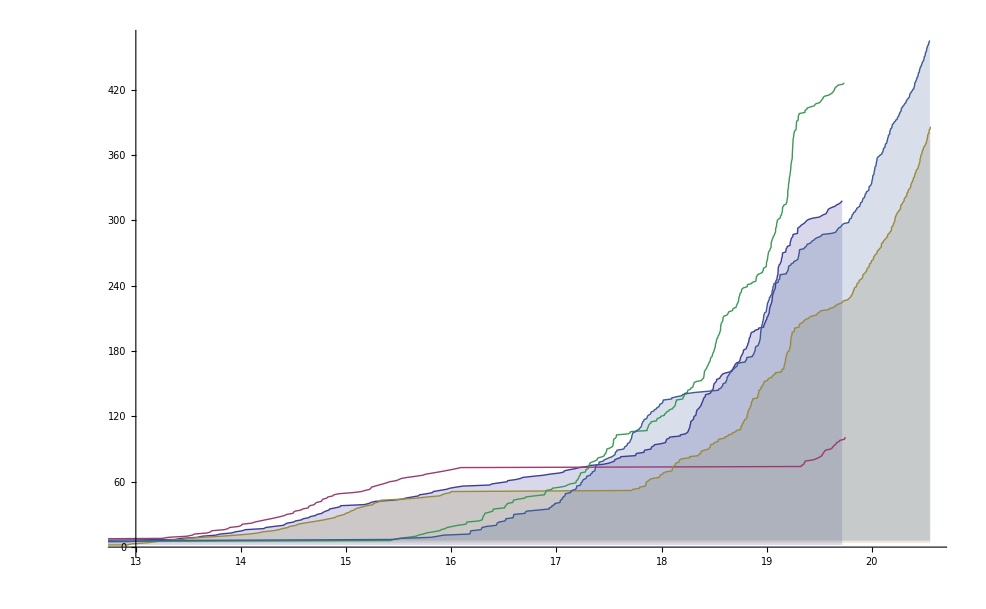

```mathematica
With[{p=3,q=5},
ListPlot[
Flatten[
Table[
With[
{zz=BinRatio[p,q,i,j,1000000000000]},
Table[{Log[zz[[k]] ],k},{k,1,Length[zz]}]
]
,{i,0,0},{j,0,q-1}
],
1],
Joined->True,
Filling->Table[{r->r+1},{r,1,p*q-1,2}]
]
]
```

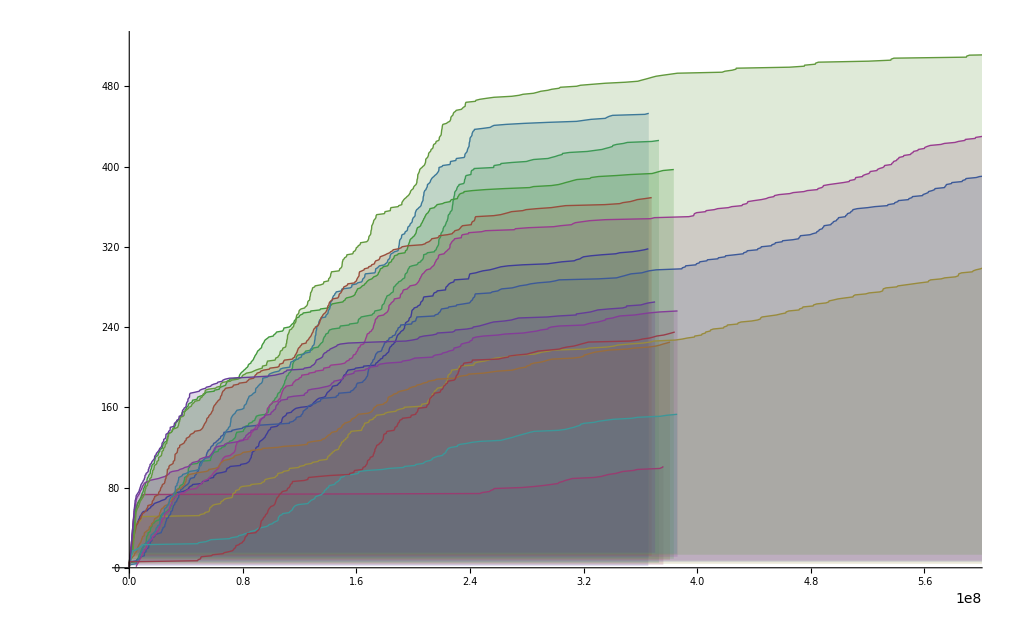

```mathematica
With[{p=3,q=5},
ListPlot[
Flatten[
Table[
With[
{zz=BinRatio[p,q,i,j,1000000000000]},
Table[{zz[[k]],k},{k,1,Length[zz]}]
]
,{i,0,p-1},{j,0,q-1}
],
1],
Joined->True,
Filling->Table[{r->r+1},{r,1,p*q-1}]
]
]
```